## Equations

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

SetOptions[ContractMetric,AllowUpperDerivatives->True];
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l}]

(*DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},FlatMetric->True,PrintAs->"g"];*)
DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},FlatMetric->False,PrintAs->"g"];

SetOptions[ContractMetric,AllowUpperDerivatives->True];

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensor[PhiC[],M4,PrintAs->"φ^*"]

DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[d][Phi[]]CD[-d][PhiC[]]]]
```

(∇_d φ^* ∇^d φ)

```mathematica
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[α]
```

```mathematica
DefTensor[n[a],M4]
DefTensor[nc[a],M4]
DefTensor[n2[a,b],M4]
DefTensor[nc2[a,b],M4]

Rulescalartovector=MakeRule[{CD[b][Phi[]],n[b]}]
Rulescalartovector2=MakeRule[{CD[b][PhiC[]],nc[b]}]

Rulevectosca=MakeRule[{n[b],CD[b][Phi[]]}]
Rulevectosca2=MakeRule[{nc[b],CD[b][PhiC[]]}]

Rule3=MakeRule[{CD[a][n[b]],n2[a,b]}]
Rule3inv=MakeRule[{n2[a,b],CD[a][n[b]]}]

Rule4=MakeRule[{CD[a][nc[b]],nc2[a,b]}]
Rule4inv=MakeRule[{nc2[a,b],CD[a][nc[b]]}]

(*ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};*)
(*rule:={Rulevectosca,Rulevectosca2,Rule3inv, Rule4inv, ruleflat}*)
rule:={Rulevectosca,Rulevectosca2,Rule3inv, Rule4inv}
```

{HoldPattern[∇^UnderBar[b̲] φ]:>Module[{},n | b
 ]}

{HoldPattern[∇^UnderBar[b̲] φ^*]:>Module[{},nc | b
 ]}

{HoldPattern[n | UnderBar[b̲]
 ]:>Module[{},∇^b φ]}

{HoldPattern[nc | UnderBar[b̲]
 ]:>Module[{},∇^b φ^*]}

{HoldPattern[∇^UnderBar[a̲] n | UnderBar[b̲]
 ]:>Module[{},n2 | a | b
  |  ]}

{HoldPattern[n2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a n | b
 ]}

{HoldPattern[∇^UnderBar[a̲] nc | UnderBar[b̲]
 ]:>Module[{},nc2 | a | b
  |  ]}

{HoldPattern[nc2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a nc | b
 ]}

### Test

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
Ltry=Sqrt[-Detmetric[]]( -X[]-mS^2 Phi[]PhiC[]+ka*RicciScalarCD[])//NoScalar
LtryC=(Ltry//NoScalar)/.Rulescalartovector/.Rulescalartovector2
```

√(-g^OverTilde[~]) (-m^2 φ φ^*+k R[∇]-∇_a φ^* ∇^a φ)

√(-g^OverTilde[~]) (-n | a
  nc |  
a-m^2 φ φ^*+k R[∇])

j^μ=dL/(d(d_μ ϕ))δϕ

```mathematica
cj=VarD[n[i]][LtryC]deltaPhi+VarD[nc[i]][LtryC]deltaPhiC/.Rulevectosca/.Rulevectosca2/.ruleflat//ContractMetric//Simplification
```

-ⅈ α (φ^* ∇_i φ-φ ∇_i φ^*)

### Test Cisterna

```mathematica
DefConstantSymbol[ka, PrintAs ->"k"];
```

```mathematica
LH=Sqrt[-Detmetric[]]*(ka*RicciScalarCD[]-(X[]-EinsteinCD[a,b]CD[-a][Phi[]]CD[-b][PhiC[]]));
LHC=(LH//NoScalar)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4
```

√(-g^OverTilde[~]) (G[∇] | a | b
  |   n |  
a nc |  
b-n | c
  nc |  
c+k R[∇])

```mathematica
(*current*)
```

j^μ=dL/(d(d_μ ϕ))δϕ+d_ν(dL/(d(d_μ d_ν ϕ))δϕ)-2d_ν(dL/(d(d_μ d_ν ϕ)))δϕ

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
cj1H=VarD[n[a]][LHC]deltaPhi+VarD[nc[a]][LHC]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2H=CD[b][(VarD[n2[a, b]][LHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LHC]deltaPhiC)]//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3H=-2CD[b][VarD[n2[a, b]][LHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LHC]]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jHDown=cj1H+cj2H+cj3H//Simplification//ContractMetric//Simplification;
jH2Down=Collect[(ContractMetric[SortCovDs[jHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{α ,eta},Simplify]
```

-ⅈ α √(-g^OverTilde[~]) (φ^* ∇_a φ-φ ∇_a φ^*+G[∇] |   |  
a | b (-φ^* ∇^b φ+φ ∇^b φ^*))

```mathematica
ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};
```

```mathematica
Simplify[%]/.ruleflat
```

1/2 ⅈ α (∇_a φ^* (2 φ+2 η ∇_b ∇^b φ)-∇_a φ (2 φ^*+2 η ∇_b ∇^b φ^*)+2 η (∇_b ∇_a φ^* ∇^b φ-∇_b ∇_a φ ∇^b φ^*))

```mathematica
Collect[%,{α ,eta},Simplify]
```

α (-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)+ⅈ η (∇_a φ^* ∇_b ∇^b φ-∇_a φ ∇_b ∇^b φ^*+∇_b ∇_a φ^* ∇^b φ-∇_b ∇_a φ ∇^b φ^*))

### Paper

```mathematica
DefConstantSymbol[Mp, PrintAs ->"Mp"];
DefConstantSymbol[L3, PrintAs ->"Λ"];
DefConstantSymbol[c4, PrintAs ->"c"];
DefConstantSymbol[d4, PrintAs ->"d"];
```

```mathematica
LP=1/2 Mp^2 RicciScalarCD[]-X[]-mS^2*PhiC[]*Phi[]+Mp/L3^3(c4 X[] RicciScalarCD[]-2 c4 (CD[-h]@CD[h]@Phi[]*CD[-f]@CD[f]@PhiC[]-CD[f]@CD[h]@Phi[]*CD[-f]@CD[-h]@PhiC[])+d4*1/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][PhiC[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][PhiC[]]]));
LHC=((LP//NoScalar)//ContractMetric)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4
```

-n | a
  nc |  
a-(2 c Mp n2 |   | h
h |   nc2 |   | f
f |)/Λ^3+(2 c Mp n2 | f | h
  |   nc2 |   |  
f | h)/Λ^3-m^2 φ φ^*+(Mp^2 R[∇])/2+(c Mp n | a
  nc |  
a R[∇])/Λ^3-(d Mp n |  
a n2 |   | c
b |   nc | b
  nc2 |   | a
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | b
b |   nc | c
  nc2 |   | a
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | c
b |   nc | a
  nc2 |   | b
c |)/(Λ^3 (n | a
  nc |  
a))-(d Mp n |  
a n2 |   | a
b |   nc | c
  nc2 |   | b
c |)/(Λ^3 (n | a
  nc |  
a))-(d Mp n |  
a n2 |   | b
b |   nc | a
  nc2 |   | c
c |)/(Λ^3 (n | a
  nc |  
a))+(d Mp n |  
a n2 |   | a
b |   nc | b
  nc2 |   | c
c |)/(Λ^3 (n | a
  nc |  
a))

```mathematica
(*current*)
```

j^μ=dL/(d(d_μ ϕ))δϕ+d_ν(dL/(d(d_μ d_ν ϕ))δϕ)-2d_ν(dL/(d(d_μ d_ν ϕ)))δϕ

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
cj1H=VarD[n[a]][LHC]deltaPhi+VarD[nc[a]][LHC]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2H=CD[b][(VarD[n2[a, b]][LHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LHC]deltaPhiC)]//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3H=-2CD[b][VarD[n2[a, b]][LHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LHC]]deltaPhiC//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jHDown=cj1H+cj2H+cj3H//Simplification//ContractMetric//Simplification;
jH2Down=Collect[(ContractMetric[SortCovDs[jHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{α ,c4,d4},Simplify]
```

α (-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)+(ⅈ c Mp (-∇_a φ^* (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (φ^* R[∇]+2 ∇_b ∇^b φ^*)-2 φ^* R[∇] |   |  
a | b ∇^b φ-2 ∇_b ∇_a φ^* ∇^b φ+2 φ R[∇] |   |  
a | b ∇^b φ^*+2 ∇_b ∇_a φ ∇^b φ^*))/Λ^3+1/(Λ^3 (∇_a φ^* ∇^a φ)^2)ⅈ d Mp ((∇_a φ^* ∇^a φ) (2 φ^* ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ+∇_b ∇_a φ^* (φ^* ∇^b φ-2 φ ∇^b φ^*) ∇_c ∇^c φ-φ^* ∇_a φ ∇_b ∇^b φ ∇_c ∇^c φ^*+∇_a φ ∇_b φ^* ∇^b φ ∇_c ∇^c φ^*+φ^* ∇_b ∇_a φ ∇^b φ ∇_c ∇^c φ^*-2 φ ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ^*-φ^* R[∇] |   |  
a | c ∇_b φ^* ∇^b φ ∇^c φ-∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ+φ R[∇] |   |  
a | c ∇_b φ^* ∇^b φ ∇^c φ^*+∇_b φ ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*-∇_a φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*-2 φ^* ∇^b φ^* ∇_c ∇_b φ ∇^c ∇_a φ-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c ∇_a φ+2 φ ∇^b φ^* ∇_c ∇_b φ^* ∇^c ∇_a φ-φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c ∇_b φ+2 φ ∇^b φ^* ∇_c ∇_a φ^* ∇^c ∇_b φ+φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c ∇^b φ+∇_a φ^* (-∇_b φ ∇^b φ ∇_c ∇^c φ^*+∇_b ∇^b φ (-φ^* ∇_c ∇^c φ+2 φ ∇_c ∇^c φ^*)+φ^* R[∇] |   |  
b | c ∇^b φ ∇^c φ+∇^b φ ∇_c ∇_b φ^* ∇^c φ-φ R[∇] |   |  
b | c ∇^b φ ∇^c φ^*+φ^* ∇_c ∇_b φ ∇^c ∇^b φ-2 φ ∇_c ∇_b φ^* ∇^c ∇^b φ)+φ^* R[∇] |   |   |   |  
a | b | c | d ∇^b φ ∇^c φ ∇^d φ^*)+∇^b φ (-φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c φ^* ∇_d ∇^d φ-φ^* ∇_a φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ^*-φ^* ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*+φ^* ∇_a φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+∇_a φ^* (φ^* ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ+∇_c ∇_b φ^* (φ ∇^c φ^* ∇_d ∇^d φ+∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))-φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ-φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*)+φ^* ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+∇_b φ^* (φ^* ∇_a φ ∇_c ∇^c φ ∇_d ∇^d φ^*-φ ∇_a φ^* ∇_c ∇^c φ ∇_d ∇^d φ^*+∇_c ∇_a φ^* ∇^c φ (-φ^* ∇_d ∇^d φ+φ ∇_d ∇^d φ^*)+∇_c ∇_a φ ∇^c φ^* (-φ^* ∇_d ∇^d φ+φ ∇_d ∇^d φ^*)+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*-φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ-φ^* ∇_a φ ∇_d ∇_c φ^* ∇^d ∇^c φ+φ ∇_a φ^* ∇_d ∇_c φ^* ∇^d ∇^c φ))))

```mathematica
(*Simplificando*)
```

```mathematica
term1=-ⅈ (SuperStar[φ] ∇_a φ-φ ∇_a SuperStar[φ])
```

-ⅈ (φ^* ∇_a φ-φ ∇_a φ^*)

```mathematica
term2=(ⅈ c Mp (-∇_a SuperStar[φ] (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (SuperStar[φ] R[∇]+2 ∇_b ∇^b SuperStar[φ])-2 SuperStar[φ] {{R[∇], {{, }, {a, b}}}} ∇^b φ-2 ∇_b ∇_a SuperStar[φ] ∇^b φ+2 φ {{R[∇], {{, }, {a, b}}}} ∇^b SuperStar[φ]+2 ∇_b ∇_a φ ∇^b SuperStar[φ]))/Λ^3;
Simplification[Numerator[term2]]
```

ⅈ c Mp (-∇_a φ^* (φ R[∇]+2 ∇_b ∇^b φ)+∇_a φ (φ^* R[∇]+2 ∇_b ∇^b φ^*)-2 φ^* R[∇] |   |  
a | b ∇^b φ-2 ∇_b ∇_a φ^* ∇^b φ+2 φ R[∇] |   |  
a | b ∇^b φ^*+2 ∇_b ∇_a φ ∇^b φ^*)

```mathematica
term3=1/(Λ^3 (∇_a SuperStar[φ] ∇^a φ)^2)ⅈ d Mp ((∇_a SuperStar[φ] ∇^a φ) (2 SuperStar[φ] ∇_b ∇_a φ ∇^b SuperStar[φ] ∇_c ∇^c φ+∇_b ∇_a SuperStar[φ] (SuperStar[φ] ∇^b φ-2 φ ∇^b SuperStar[φ]) ∇_c ∇^c φ-SuperStar[φ] ∇_a φ ∇_b ∇^b φ ∇_c ∇^c SuperStar[φ]+∇_a φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇^c SuperStar[φ]+SuperStar[φ] ∇_b ∇_a φ ∇^b φ ∇_c ∇^c SuperStar[φ]-2 φ ∇_b ∇_a φ ∇^b SuperStar[φ] ∇_c ∇^c SuperStar[φ]-SuperStar[φ] {{R[∇], {{, }, {a, c}}}} ∇_b SuperStar[φ] ∇^b φ ∇^c φ-∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ+φ {{R[∇], {{, }, {a, c}}}} ∇_b SuperStar[φ] ∇^b φ ∇^c SuperStar[φ]+∇_b φ ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-∇_a φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]-2 SuperStar[φ] ∇^b SuperStar[φ] ∇_c ∇_b φ ∇^c ∇_a φ-SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c ∇_a φ+2 φ ∇^b SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c ∇_a φ-SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c ∇_b φ+2 φ ∇^b SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c ∇_b φ+SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c ∇^b φ+∇_a SuperStar[φ] (-∇_b φ ∇^b φ ∇_c ∇^c SuperStar[φ]+∇_b ∇^b φ (-SuperStar[φ] ∇_c ∇^c φ+2 φ ∇_c ∇^c SuperStar[φ])+SuperStar[φ] {{R[∇], {{, }, {b, c}}}} ∇^b φ ∇^c φ+∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ-φ {{R[∇], {{, }, {b, c}}}} ∇^b φ ∇^c SuperStar[φ]+SuperStar[φ] ∇_c ∇_b φ ∇^c ∇^b φ-2 φ ∇_c ∇_b SuperStar[φ] ∇^c ∇^b φ)+SuperStar[φ] {{R[∇], {{, , , }, {a, b, c, d}}}} ∇^b φ ∇^c φ ∇^d SuperStar[φ])+∇^b φ (-SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇^d φ-SuperStar[φ] ∇_a φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇^d SuperStar[φ]-SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_b ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+∇_a SuperStar[φ] (SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇^d φ+∇_c ∇_b SuperStar[φ] (φ ∇^c SuperStar[φ] ∇_d ∇^d φ+∇^c φ (SuperStar[φ] ∇_d ∇^d φ-φ ∇_d ∇^d SuperStar[φ]))-SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ-SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ])+SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+∇_b SuperStar[φ] (SuperStar[φ] ∇_a φ ∇_c ∇^c φ ∇_d ∇^d SuperStar[φ]-φ ∇_a SuperStar[φ] ∇_c ∇^c φ ∇_d ∇^d SuperStar[φ]+∇_c ∇_a SuperStar[φ] ∇^c φ (-SuperStar[φ] ∇_d ∇^d φ+φ ∇_d ∇^d SuperStar[φ])+∇_c ∇_a φ ∇^c SuperStar[φ] (-SuperStar[φ] ∇_d ∇^d φ+φ ∇_d ∇^d SuperStar[φ])+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-SuperStar[φ] ∇_a φ ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ+φ ∇_a SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ)))//NoScalar;
tem=Simplification[Numerator[term3]]
```

-ⅈ d Mp ∇^b φ (φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c φ^* ∇_d ∇^d φ+φ^* ∇_a φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ^*+φ^* ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*-∇_b φ ∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*-φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*-φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*-φ^* ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*+φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*+φ ∇_b ∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇_a φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ^* ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+∇_a φ^* (-φ^* ∇_c ∇_b φ ∇^c φ^* ∇_d ∇^d φ+∇_b φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*-∇_c ∇_b φ^* (φ ∇^c φ^* ∇_d ∇^d φ+∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ+φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*+∇_b φ^* (∇_c ∇^c φ (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*)-∇^c φ ∇_d ∇_c φ^* ∇^d φ+R[∇] |   |  
c | d ∇^c φ (-φ^* ∇^d φ+φ ∇^d φ^*)-φ^* ∇_d ∇_c φ ∇^d ∇^c φ+φ ∇_d ∇_c φ^* ∇^d ∇^c φ))+∇_b φ^* (-∇_a φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*+φ ∇_c ∇_a φ^* (2 ∇^c φ^* ∇_d ∇^d φ-∇^c φ ∇_d ∇^d φ^*)-∇_c ∇_a φ (φ^* ∇^c φ ∇_d ∇^d φ^*+∇^c φ^* (φ^* ∇_d ∇^d φ-φ ∇_d ∇^d φ^*))+φ^* R[∇] |   |  
a | d ∇_c φ^* ∇^c φ ∇^d φ+∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ-φ R[∇] |   |  
a | d ∇_c φ^* ∇^c φ ∇^d φ^*+∇_a φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*+φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ-2 φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ+φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*+φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ-φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ-φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*))

```mathematica
-ⅈ d Mp ∇^b φ (SuperStar[φ] ∇_a φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ] Bϕ+SuperStar[φ] ∇_a φ ∇_c ∇_b φ ∇^c SuperStar[φ]BϕC+SuperStar[φ] ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]-∇_b φ ∇_c SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]-SuperStar[φ] ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]+φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]+φ ∇_b ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-SuperStar[φ] ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+∇_a SuperStar[φ] (-SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ] Bϕ+∇_b φ ∇_c SuperStar[φ] ∇^c φ BϕC-∇_c ∇_b SuperStar[φ] (φ ∇^c SuperStar[φ] Bϕ+∇^c φ (SuperStar[φ]Bϕ-φ BϕC))+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ+SuperStar[φ] ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ]+∇_b SuperStar[φ] (BϕC (SuperStar[φ]BϕC-φ BϕC)-∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d φ+{{R[∇], {{, }, {c, d}}}} ∇^c φ (-SuperStar[φ] ∇^d φ+φ ∇^d SuperStar[φ])-SuperStar[φ] ∇_d ∇_c φ ∇^d ∇^c φ+φ ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ))+∇_b SuperStar[φ] (-∇_a φ ∇_c SuperStar[φ] ∇^c φ  BϕC+φ ∇_c ∇_a SuperStar[φ] (2 ∇^c SuperStar[φ]Bϕ-∇^c φ  BϕC)-∇_c ∇_a φ (SuperStar[φ] ∇^c φ  BϕC+∇^c SuperStar[φ] (SuperStar[φ]Bϕ-φ  BϕC))+SuperStar[φ] {{R[∇], {{, }, {a, d}}}} XX∇^d φ+XX ∇_d ∇_a SuperStar[φ] ∇^d φ-φ {{R[∇], {{, }, {a, d}}}} XX ∇^d SuperStar[φ]+∇_a φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ-2 φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ+φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]+SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ-SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} ∇^c φ ∇^d φ ∇^e SuperStar[φ]))//Expand
```

```mathematica
ⅈ BϕC^2 d Mp φ ∇_a SuperStar[φ] XX-ⅈ BϕC^2 d Mp SuperStar[φ] ∇_a SuperStar[φ] XX-ⅈ BϕC d Mp ∇_a SuperStar[φ] ∇_b φ ∇^b φ ∇_c SuperStar[φ] ∇^c φ+ⅈ BϕC d Mp ∇_a φ XX XX+ⅈ BϕC d Mp SuperStar[φ] XX ∇_c ∇_a φ ∇^c φ+ⅈ BϕC d Mp φ XX ∇_c ∇_a SuperStar[φ] ∇^c φ-ⅈ BϕC d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ+ⅈ Bϕ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ-ⅈ BϕC d Mp φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ]+ⅈ Bϕ d Mp SuperStar[φ] XX ∇_c ∇_a φ ∇^c SuperStar[φ]-2 ⅈ Bϕ d Mp φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-ⅈ BϕC d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ]+ⅈ Bϕ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ]-ⅈ Bϕ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]+ⅈ Bϕ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c SuperStar[φ]-ⅈ d Mp XX SuperStar[φ] {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d φ+ⅈ d Mp SuperStar[φ] {{R[∇], {{, }, {c, d}}}} ∇_a SuperStar[φ] XX ∇^c φ ∇^d φ-ⅈ d Mp XX ∇_b SuperStar[φ] ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d φ+ⅈ d Mp ∇_a SuperStar[φ] XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d φ+ⅈ d Mp XX φ {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d SuperStar[φ]-ⅈ d Mp φ {{R[∇], {{, }, {c, d}}}} ∇_a SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇^d SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+ⅈ d Mp ∇_b φ ∇^b φ XX ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+ⅈ d Mp SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-ⅈ d Mp φ ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp ∇_a φ XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp φ ∇_b ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-ⅈ d Mp SuperStar[φ] XX ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+2 ⅈ d Mp φ XX ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-ⅈ d Mp φ XX ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_b φ-ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+ⅈ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ-ⅈ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+ⅈ d Mp φ ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ]-ⅈ d Mp SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp φ XX ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp SuperStar[φ] ∇_a φ ∇^b φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ+ⅈ d Mp SuperStar[φ] ∇_a SuperStar[φ] XX ∇_d ∇_c φ ∇^d ∇^c φ-ⅈ d Mp φ ∇_a SuperStar[φ] XX ∇_d ∇_c SuperStar[φ] ∇^d ∇^c φ+ⅈ d Mp SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} XX ∇^c φ ∇^d φ ∇^e SuperStar[φ]//FullSimplify
```

ⅈ d Mp (BϕC XX φ^* ∇_c ∇_a φ ∇^c φ+BϕC XX φ ∇_c ∇_a φ^* ∇^c φ+Bϕ XX φ^* ∇_c ∇_a φ ∇^c φ^*-BϕC φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*-2 Bϕ φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*-XX φ^* R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ-XX ∇_b φ^* ∇^b φ ∇_d ∇_a φ^* ∇^d φ+XX φ R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ^*-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+XX ∇_b φ ∇^b φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇^b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-XX φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+2 XX φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ-XX φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*-φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ+XX φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+∇_a φ (XX (BϕC XX-∇^c φ ∇_d ∇_c φ^* ∇^d φ^*)+φ^* ∇^b φ ∇^c φ^* (-BϕC ∇_c ∇_b φ-Bϕ ∇_c ∇_b φ^*+∇_d ∇_c φ^* ∇^d ∇_b φ+∇_d ∇_b φ^* ∇^d ∇_c φ))+∇_a φ^* (-BϕC ∇_b φ ∇^b φ ∇_c φ^* ∇^c φ-∇^b φ (-Bϕ φ^* ∇_c ∇_b φ ∇^c φ^*+∇_c ∇_b φ^* ((BϕC φ-Bϕ φ^*) ∇^c φ-Bϕ φ ∇^c φ^*)+φ R[∇] |   |  
c | d ∇_b φ^* ∇^c φ ∇^d φ^*+(φ^* ∇^c φ^* ∇_d ∇_c φ+(φ^* ∇^c φ+φ ∇^c φ^*) ∇_d ∇_c φ^*) ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*)+XX (BϕC^2 (φ-φ^*)+φ^* R[∇] |   |  
c | d ∇^c φ ∇^d φ+φ^* ∇_d ∇_c φ ∇^d ∇^c φ+∇_d ∇_c φ^* (∇^c φ ∇^d φ-φ ∇^d ∇^c φ)))+XX φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*)

```mathematica
Collect[(BϕC XX SuperStar[φ] ∇_c ∇_a φ ∇^c φ+BϕC XX φ ∇_c ∇_a SuperStar[φ] ∇^c φ+Bϕ XX SuperStar[φ] ∇_c ∇_a φ ∇^c SuperStar[φ]-BϕC φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ]-2 Bϕ φ ∇_b SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c SuperStar[φ]-XX SuperStar[φ] {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d φ-XX ∇_b SuperStar[φ] ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d φ+XX φ {{R[∇], {{, }, {a, d}}}} ∇_b SuperStar[φ] ∇^b φ ∇^d SuperStar[φ]-SuperStar[φ] ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a φ ∇^d SuperStar[φ]+XX ∇_b φ ∇^b φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇^b φ ∇_c ∇_b SuperStar[φ] ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+φ ∇^b φ ∇_c ∇_b φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d SuperStar[φ]+SuperStar[φ] ∇^b φ ∇_c ∇_a SuperStar[φ] ∇^c φ ∇_d ∇_b φ ∇^d SuperStar[φ]-φ ∇^b φ ∇_c ∇_a φ ∇^c SuperStar[φ] ∇_d ∇_b SuperStar[φ] ∇^d SuperStar[φ]-φ ∇_b ∇_a SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ]-XX SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ ∇^d ∇_a φ+2 XX φ ∇^c SuperStar[φ] ∇_d ∇_c SuperStar[φ] ∇^d ∇_a φ-XX φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_a SuperStar[φ]-SuperStar[φ] ∇_b SuperStar[φ] ∇^b φ ∇^c φ ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+XX φ ∇^c SuperStar[φ] ∇_d ∇_a SuperStar[φ] ∇^d ∇_c φ+∇_a φ (XX (BϕC XX-∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d SuperStar[φ])+SuperStar[φ] ∇^b φ ∇^c SuperStar[φ] (-BϕC ∇_c ∇_b φ-Bϕ ∇_c ∇_b SuperStar[φ]+∇_d ∇_c SuperStar[φ] ∇^d ∇_b φ+∇_d ∇_b SuperStar[φ] ∇^d ∇_c φ))+∇_a SuperStar[φ] (-BϕC ∇_b φ ∇^b φ ∇_c SuperStar[φ] ∇^c φ-∇^b φ (-Bϕ SuperStar[φ] ∇_c ∇_b φ ∇^c SuperStar[φ]+∇_c ∇_b SuperStar[φ] ((BϕC φ-Bϕ SuperStar[φ]) ∇^c φ-Bϕ φ ∇^c SuperStar[φ])+φ {{R[∇], {{, }, {c, d}}}} ∇_b SuperStar[φ] ∇^c φ ∇^d SuperStar[φ]+(SuperStar[φ] ∇^c SuperStar[φ] ∇_d ∇_c φ+(SuperStar[φ] ∇^c φ+φ ∇^c SuperStar[φ]) ∇_d ∇_c SuperStar[φ]) ∇^d ∇_b φ-φ ∇^c φ ∇_d ∇_c SuperStar[φ] ∇^d ∇_b SuperStar[φ])+XX (BϕC^2 (φ-SuperStar[φ])+SuperStar[φ] {{R[∇], {{, }, {c, d}}}} ∇^c φ ∇^d φ+SuperStar[φ] ∇_d ∇_c φ ∇^d ∇^c φ+∇_d ∇_c SuperStar[φ] (∇^c φ ∇^d φ-φ ∇^d ∇^c φ)))+XX SuperStar[φ] {{R[∇], {{, , , }, {a, c, d, e}}}} ∇^c φ ∇^d φ ∇^e SuperStar[φ])//Expand,{BϕC,Bϕ,XX}]
```

BϕC^2 XX (φ ∇_a φ^*-φ^* ∇_a φ^*)+BϕC (XX^2 ∇_a φ-∇_a φ^* ∇_b φ ∇^b φ ∇_c φ^* ∇^c φ-φ ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ+XX (φ^* ∇_c ∇_a φ ∇^c φ+φ ∇_c ∇_a φ^* ∇^c φ)-φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*-φ^* ∇_a φ ∇^b φ ∇_c ∇_b φ ∇^c φ^*)+Bϕ (φ^* ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ+XX φ^* ∇_c ∇_a φ ∇^c φ^*-2 φ ∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ^*+φ^* ∇_a φ^* ∇^b φ ∇_c ∇_b φ ∇^c φ^*-φ^* ∇_a φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*+φ ∇_a φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ^*)-φ R[∇] |   |  
c | d ∇_a φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇^d φ^*-φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d φ^*+φ ∇^b φ ∇_c ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d φ^*+φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*-φ ∇^b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d φ^*-φ ∇_b ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇_a φ^* ∇^b φ ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_b φ-φ^* ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ+φ^* ∇_a φ ∇^b φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ-φ ∇_a φ^* ∇^b φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_b φ+φ ∇_a φ^* ∇^b φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_b φ^*-φ^* ∇_b φ^* ∇^b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ+φ^* ∇_a φ ∇^b φ ∇^c φ^* ∇_d ∇_b φ^* ∇^d ∇_c φ+XX (-φ^* R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ+φ^* R[∇] |   |  
c | d ∇_a φ^* ∇^c φ ∇^d φ-∇_b φ^* ∇^b φ ∇_d ∇_a φ^* ∇^d φ+∇_a φ^* ∇^c φ ∇_d ∇_c φ^* ∇^d φ+φ R[∇] |   |  
a | d ∇_b φ^* ∇^b φ ∇^d φ^*+∇_b φ ∇^b φ ∇_d ∇_a φ^* ∇^d φ^*-∇_a φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*-φ^* ∇^c φ^* ∇_d ∇_c φ ∇^d ∇_a φ+2 φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ-φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*+φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+φ^* ∇_a φ^* ∇_d ∇_c φ ∇^d ∇^c φ-φ ∇_a φ^* ∇_d ∇_c φ^* ∇^d ∇^c φ+φ^* R[∇] |   |   |   |  
a | c | d | e ∇^c φ ∇^d φ ∇^e φ^*)

```mathematica
(*ContractMetric[SortCovDs[tem,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplify *)
```

```mathematica
(*Flat Space*)
```

```mathematica
ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};
```

```mathematica
Simplify[%]/.ruleflat
```

```mathematica
Collect[%,{α ,eta},Simplify]
```

### Metric

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
(*MatrixForm[metricarray={{-1,0,0,0},{0,1,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]*)
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
MetricInBasis[metric,-esf,metricarray]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];

ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
```

```mathematica
ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];
```

```mathematica
j1=term1//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

term1

```mathematica
j2=term2//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-(4 c Mp w (gg[r]^3 NN[r] ϕ[r]^2+NN[r] r ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2),0,0,0}

```mathematica
org[expr_]:=ToValues@ToValues@ComponentArray@ToValues@TraceBasisDummy@ToBasis[esf]@Implode@expr
evalScalar=Scalar[cont_]:>org@cont;
```

```mathematica
noScalar=Scalar[cont_]:>NoScalar[cont];
```

```mathematica
term3/.evalScalar//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-(8 d Mp w NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 gg[r]^3 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),(8 ⅈ d Mp w^2 ϕ[r]^2 ϕ'[r]^2)/(Λ^3 w^2 gg[r]^2 r ϕ[r]^2-Λ^3 NN[r]^2 r ϕ'[r]^2),0,0}

```mathematica
jHup=(metric[a, b]jH2Down)/.evalScalar//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{(2 w α (w^4 gg[r]^7 NN[r] (2 c Mp-Λ^3 r^2) ϕ[r]^6-2 c Mp w^4 gg[r]^4 NN[r] r ϕ[r]^5 gg'[r] (-2 ϕ[r]+r ϕ'[r])+4 c Mp w^2 gg[r]^2 NN[r]^3 r ϕ[r]^3 gg'[r] ϕ'[r]^2 (-2 ϕ[r]+r ϕ'[r])+2 Mp NN[r]^5 r ϕ[r] gg'[r] ϕ'[r]^4 (2 (c+d) ϕ[r]-c r ϕ'[r])+gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (4 c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (2 c Mp-Λ^3 r^2) ϕ'[r]^2+4 c Mp w^2 NN[r] (ϕ[r]^2-r^2 ϕ'[r]^2-r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 w^2 gg[r]^5 ϕ[r]^4 (-c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (-2 c Mp+Λ^3 r^2) ϕ'[r]^2+c Mp w^2 NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 Mp gg[r] NN[r]^4 ϕ'[r]^3 (r ϕ[r] NN'[r] ϕ'[r] (2 d ϕ[r]-c r ϕ'[r])+NN[r] (c r^2 ϕ'[r]^3+r ϕ[r] ϕ'[r] (2 (c+d) ϕ'[r]+c r ϕ''[r])-ϕ[r]^2 (c ϕ'[r]+2 d r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),(8 ⅈ d Mp w^2 α ϕ[r]^2 ϕ'[r]^2)/(Λ^3 w^2 gg[r]^4 r ϕ[r]^2-Λ^3 gg[r]^2 NN[r]^2 r ϕ'[r]^2),0,0}

```mathematica
jH=jH2Down/.evalScalar//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

{-((2 w α (w^4 gg[r]^7 NN[r] (2 c Mp-Λ^3 r^2) ϕ[r]^6-2 c Mp w^4 gg[r]^4 NN[r] r ϕ[r]^5 gg'[r] (-2 ϕ[r]+r ϕ'[r])+4 c Mp w^2 gg[r]^2 NN[r]^3 r ϕ[r]^3 gg'[r] ϕ'[r]^2 (-2 ϕ[r]+r ϕ'[r])+2 Mp NN[r]^5 r ϕ[r] gg'[r] ϕ'[r]^4 (2 (c+d) ϕ[r]-c r ϕ'[r])+gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (4 c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (2 c Mp-Λ^3 r^2) ϕ'[r]^2+4 c Mp w^2 NN[r] (ϕ[r]^2-r^2 ϕ'[r]^2-r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 w^2 gg[r]^5 ϕ[r]^4 (-c Mp w^2 r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r]^3 (-2 c Mp+Λ^3 r^2) ϕ'[r]^2+c Mp w^2 NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 Mp gg[r] NN[r]^4 ϕ'[r]^3 (r ϕ[r] NN'[r] ϕ'[r] (2 d ϕ[r]-c r ϕ'[r])+NN[r] (c r^2 ϕ'[r]^3+r ϕ[r] ϕ'[r] (2 (c+d) ϕ'[r]+c r ϕ''[r])-ϕ[r]^2 (c ϕ'[r]+2 d r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)),(8 ⅈ d Mp w^2 α ϕ[r]^2 ϕ'[r]^2)/(Λ^3 w^2 gg[r]^2 r ϕ[r]^2-Λ^3 NN[r]^2 r ϕ'[r]^2),0,0}

```mathematica
j0H=Collect[jHup[[1]],{α,c4, d4},Simplify]//Simplify
```

2 w α (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 gg[r]^3 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+NN[r] r ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 gg[r]^3 NN[r] r^2))

```mathematica
j0Hup=Collect[jH[[1]],{α,c4, d4},Simplify]//Simplify
```

```mathematica
Int2=j0H/.{r[]-> r,θ[]-> θ}
```

2 w α (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 r gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]))

```mathematica
Sqrt[-Detmetric[]]//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

√(gg[r]^2 NN[r]^2 r^4 Sin[θ]^2)

## Tensor Manipulation

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;
(* evita que salgan los indices feos *)
$CommuteCovDsOnScalars=True;
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]
```

((▽_a φ^*) (▽^a φ))

```mathematica
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[Mp, PrintAs ->"Mp"];
DefConstantSymbol[L3, PrintAs ->"Λ"];
DefConstantSymbol[c4, PrintAs ->"c"];
DefConstantSymbol[d4, PrintAs ->"d"];
DefConstantSymbol[ka, PrintAs ->"k"]
```

```mathematica
L=Sqrt[-Detmetric[]]*(1/2 Mp^2 RicciScalarCD[]-X[]-mS^2*PhiC[]*Phi[]+Mp/L3^3(c4 X[] RicciScalarCD[]-2 c4 (CD[-h]@CD[h]@Phi[]*CD[-f]@CD[f]@PhiC[]-CD[f]@CD[h]@Phi[]*CD[-f]@CD[-h]@PhiC[])+d4*1/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][PhiC[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][PhiC[]]])));
```

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation[L/.d4-> 0];
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification
```

(-Λ^3 m^2 φ^*+(Λ^3-c Mp R[▽]) (▽_a▽^a φ^*)-c Mp (▽_a R[▽]) (▽^a φ^*)+2 c Mp (▽_b▽_a▽^b▽^a φ^*)-2 c Mp (▽_b▽^b▽_a▽^a φ^*))/Λ^3

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //RicciToEinstein//Simplification //ContractMetric
```

-m^2 φ^*+▽_a▽^a φ^*+(2 c Mp G[▽] | a | b
  |   (▽_b▽_a φ^*))/Λ^3

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-VarD[metpert[LI[1],a,b],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical;(*//Simplification//Simplify;*)
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical (*//RicciToEinstein//Simplification*);
```

```mathematica
Ecu=Collect[Ecu, {c4, L3},Simplify]
```

1/2 (Mp^2 G[▽] |   |  
a | b-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (m^2 φ φ^*+(▽_c φ^*) (▽^c φ)))+1/(2 Λ^3)c Mp ((▽_a φ^*) (R[▽] (▽_b φ)-2 R[▽] |   |  
b | c (▽^c φ))+(▽_a φ) (R[▽] (▽_b φ^*)-2 R[▽] |   |  
b | c (▽^c φ^*))+2 ((▽_b▽_a φ^*) (▽_c▽^c φ)+(▽_b▽_a φ) (▽_c▽^c φ^*)-R[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)+G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)-R[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)-(▽_c▽_b φ^*) (▽^c▽_a φ)-(▽_c▽_a φ^*) (▽^c▽_b φ)-g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)+2 g |   |  
a | b R[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)+g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)))

```mathematica
<<xAct`xTras`
```

```mathematica
$Info=False;
$CVVerbose=False;
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]

ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];
```

```mathematica
Hesfϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

1/(Λ^3 gg[r]^5 NN[r]^2 r^2)ⅇ^(-ⅈ w t) (gg[r]^5 (-Λ^3 m^2 NN[r]^2 r^2+w^2 (-2 c Mp+Λ^3 r^2)) ϕ[r]-6 c Mp NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]-gg[r]^2 gg'[r] (4 c Mp w^2 r ϕ[r]+NN[r]^2 (-2 c Mp+Λ^3 r^2) ϕ'[r])+2 c Mp gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (2 c Mp w^2 ϕ[r]+NN[r] ((-2 c Mp+Λ^3 r^2) NN'[r] ϕ'[r]+NN[r] (2 Λ^3 r ϕ'[r]+(-2 c Mp+Λ^3 r^2) ϕ''[r]))))

```mathematica
eqϕ=Collect[Hesfϕ*Λ^3 gg[r]^5 NN[r]^2 r^2*ⅇ^(ⅈ w t),{c4,L3}, Simplify]
```

Λ^3 gg[r]^2 r (gg[r]^3 (w^2-m^2 NN[r]^2) r ϕ[r]-NN[r]^2 r gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 w^2 r ϕ[r]+NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r]))+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))

```mathematica
Hesf=Ecu//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

{{1/(2 Λ^3 gg[r]^5 r^2)(gg[r]^5 (w^2 (2 c Mp-Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp gg[r]^2 r (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2) gg'[r]-12 c Mp NN[r]^2 r gg'[r] ϕ'[r]^2-gg[r]^3 (2 c Mp w^2 ϕ[r]^2+NN[r]^2 (Λ^3 Mp^2+(-2 c Mp+Λ^3 r^2) ϕ'[r]^2))+2 c Mp gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r])),0,0,0},{0,1/(2 Λ^3 gg[r]^2 NN[r]^3 r^2)(gg[r]^4 (w^2 NN[r] (2 c Mp-Λ^3 r^2) ϕ[r]^2+Λ^3 NN[r]^3 (-Mp^2+m^2 r^2 ϕ[r]^2))-6 c Mp NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 Λ^3 Mp^2 NN[r]^2 r NN'[r]+4 c Mp w^2 r ϕ[r]^2 NN'[r]-2 c Mp w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^3 (Λ^3 Mp^2+(2 c Mp-Λ^3 r^2) ϕ'[r]^2))),0,0},{0,0,1/(2 Λ^3 gg[r]^5 NN[r]^4)r (Λ^3 gg[r]^5 NN[r]^2 (-w^2+m^2 NN[r]^2) r ϕ[r]^2+6 c Mp NN[r]^3 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^2-Mp gg[r]^2 NN[r] gg'[r] (Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-2 c w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))-2 c Mp gg[r] NN[r]^3 ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-4 c Mp w^2 r ϕ[r]^2 NN'[r]^2+Λ^3 NN[r]^4 r ϕ'[r]^2+Λ^3 Mp^2 NN[r]^3 (NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))-4 c Mp w^2 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))),0},{0,0,0,1/(2 Λ^3 gg[r]^5 NN[r]^4)r Sin[θ]^2 (Λ^3 gg[r]^5 NN[r]^2 (-w^2+m^2 NN[r]^2) r ϕ[r]^2+6 c Mp NN[r]^3 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^2-Mp gg[r]^2 NN[r] gg'[r] (Λ^3 Mp NN[r]^3+Λ^3 Mp NN[r]^2 r NN'[r]+2 c w^2 r ϕ[r]^2 NN'[r]-2 c w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))-2 c Mp gg[r] NN[r]^3 ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (-4 c Mp w^2 r ϕ[r]^2 NN'[r]^2+Λ^3 NN[r]^4 r ϕ'[r]^2+Λ^3 Mp^2 NN[r]^3 (NN'[r]+r NN''[r])+2 c Mp w^2 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))-4 c Mp w^2 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r]))))}}

The 00-11 equations are

```mathematica
Eq00=Collect[Hesf[[1]][[1]]*(2 Λ^3 gg[r]^5 r^2),{c4,L3}, Simplify]
```

Λ^3 gg[r]^2 (gg[r]^3 (-w^2 r^2 ϕ[r]^2+NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp^2 NN[r]^2 r gg'[r]-gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 w^2 gg[r]^2 r ϕ[r]^2 gg'[r]-6 NN[r]^2 r gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))

```mathematica
Eq11=Collect[Hesf[[2]][[2]]*(2 Λ^3 gg[r]^2 NN[r]^3 r^2),{c4,L3}, Simplify]
```

Λ^3 gg[r]^2 NN[r] (-w^2 gg[r]^2 r^2 ϕ[r]^2+2 Mp^2 NN[r] r NN'[r]+NN[r]^2 (Mp^2+gg[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)-r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 w^2 r ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))

### Solved the System of equation

```mathematica
Dgg=Solve[Eq00==0/.{r[]-> r},{D[gg[r],r]}][[1,1]]/.Rule->Equal
DNN=Solve[Eq11==0/.{r[]-> r},{D[NN[r],r]}][[1,1]]/.Rule->Equal//FullSimplify
DDPhi=Solve[eqϕ==0/.{r[]-> r},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

gg'[r]==(Λ^3 Mp^2 gg[r]^3 NN[r]^2-Λ^3 Mp^2 gg[r]^5 NN[r]^2+2 c Mp w^2 gg[r]^3 ϕ[r]^2-2 c Mp w^2 gg[r]^5 ϕ[r]^2+Λ^3 r^2 w^2 gg[r]^5 ϕ[r]^2+Λ^3 m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2-2 c Mp gg[r] NN[r]^2 ϕ'[r]^2-2 c Mp gg[r]^3 NN[r]^2 ϕ'[r]^2+Λ^3 r^2 gg[r]^3 NN[r]^2 ϕ'[r]^2-8 c Mp r gg[r] NN[r]^2 ϕ'[r] ϕ''[r])/(2 Mp r (Λ^3 Mp gg[r]^2 NN[r]^2+2 c w^2 gg[r]^2 ϕ[r]^2-6 c NN[r]^2 ϕ'[r]^2))

NN'[r]==(NN[r] (gg[r]^4 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))+6 c Mp NN[r]^2 ϕ'[r]^2+gg[r]^2 (2 c Mp w^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-Λ^3 Mp^2+(-2 c Mp+Λ^3 r^2) ϕ'[r]^2))))/(2 Mp r (gg[r]^2 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2)-6 c NN[r]^2 ϕ'[r]^2))

ϕ''[r]==(gg[r]^5 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]-6 c Mp NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]-gg[r]^2 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+gg[r]^3 (2 c Mp w^2 ϕ[r]+NN[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r])+2 c Mp gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))/(gg[r] NN[r] ((-2 c Mp+(2 c Mp-Λ^3 r^2) gg[r]^2) NN[r]-4 c Mp r NN'[r]))

```mathematica
SDgg=Eq00==0/.{r[]-> r}
SDNN=Eq11==0/.{r[]-> r}
SDDPhi=eqϕ==0/.{r[]-> r}
```

Λ^3 gg[r]^2 (gg[r]^3 (-r^2 w^2 ϕ[r]^2+NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp^2 r NN[r]^2 gg'[r]-gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))==0

Λ^3 gg[r]^2 NN[r] (-r^2 w^2 gg[r]^2 ϕ[r]^2+2 Mp^2 r NN[r] NN'[r]+NN[r]^2 (Mp^2+gg[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)-r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))==0

Λ^3 r gg[r]^2 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 ϕ[r]+NN[r]^2 ϕ'[r])+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))==0

## Computing X

```mathematica
Quit[]
```

### Computing the Energy and Particle Number

```mathematica
Dgg=gg'[r]==(Λ^3 Mp^2 gg[r]^3 NN[r]^2-Λ^3 Mp^2 gg[r]^5 NN[r]^2+2 c Mp w^2 gg[r]^3 ϕ[r]^2-2 c Mp w^2 gg[r]^5 ϕ[r]^2+Λ^3 r^2 w^2 gg[r]^5 ϕ[r]^2+Λ^3 m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2-2 c Mp gg[r] NN[r]^2 ϕ'[r]^2-2 c Mp gg[r]^3 NN[r]^2 ϕ'[r]^2+Λ^3 r^2 gg[r]^3 NN[r]^2 ϕ'[r]^2-8 c Mp r gg[r] NN[r]^2 ϕ'[r] ϕ''[r])/(2 Mp r (Λ^3 Mp gg[r]^2 NN[r]^2+2 c w^2 gg[r]^2 ϕ[r]^2-6 c NN[r]^2 ϕ'[r]^2));

DNN=NN'[r]==(NN[r] (gg[r]^4 ((-2 c Mp+Λ^3 r^2) w^2 ϕ[r]^2+Λ^3 NN[r]^2 (Mp-m r ϕ[r]) (Mp+m r ϕ[r]))+6 c Mp NN[r]^2 ϕ'[r]^2+gg[r]^2 (2 c Mp w^2 ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-Λ^3 Mp^2+(-2 c Mp+Λ^3 r^2) ϕ'[r]^2))))/(2 Mp r (gg[r]^2 (Λ^3 Mp NN[r]^2+2 c w^2 ϕ[r]^2)-6 c NN[r]^2 ϕ'[r]^2));

DDPhi=ϕ''[r]==(gg[r]^5 ((-2 c Mp+Λ^3 r^2) w^2-Λ^3 m^2 r^2 NN[r]^2) ϕ[r]-6 c Mp NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]-gg[r]^2 gg'[r] (4 c Mp r w^2 ϕ[r]+(-2 c Mp+Λ^3 r^2) NN[r]^2 ϕ'[r])+gg[r]^3 (2 c Mp w^2 ϕ[r]+NN[r] (2 Λ^3 r NN[r]+(-2 c Mp+Λ^3 r^2) NN'[r]) ϕ'[r])+2 c Mp gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))/(gg[r] NN[r] ((-2 c Mp+(2 c Mp-Λ^3 r^2) gg[r]^2) NN[r]-4 c Mp r NN'[r]));
```

```mathematica
SeqN=Λ^3 gg[r]^2 (gg[r]^3 (-r^2 w^2 ϕ[r]^2+NN[r]^2 (Mp^2-m^2 r^2 ϕ[r]^2))+2 Mp^2 r NN[r]^2 gg'[r]-gg[r] NN[r]^2 (Mp^2+r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^5 ϕ[r]^2+2 r w^2 gg[r]^2 ϕ[r]^2 gg'[r]-6 r NN[r]^2 gg'[r] ϕ'[r]^2+gg[r]^3 (-w^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+gg[r] NN[r]^2 ϕ'[r] (ϕ'[r]+4 r ϕ''[r]))==0;

Seqg=Λ^3 gg[r]^2 NN[r] (-r^2 w^2 gg[r]^2 ϕ[r]^2+2 Mp^2 r NN[r] NN'[r]+NN[r]^2 (Mp^2+gg[r]^2 (-Mp^2+m^2 r^2 ϕ[r]^2)-r^2 ϕ'[r]^2))+2 c Mp (w^2 gg[r]^4 NN[r] ϕ[r]^2-3 NN[r]^2 (NN[r]+2 r NN'[r]) ϕ'[r]^2+gg[r]^2 (2 r w^2 ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2-w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r])))==0;

Seqphi=Λ^3 r gg[r]^2 (r gg[r]^3 (w^2-m^2 NN[r]^2) ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 c Mp (-w^2 gg[r]^5 ϕ[r]-3 NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 ϕ[r]+NN[r]^2 ϕ'[r])+gg[r] NN[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r]))+gg[r]^3 (w^2 ϕ[r]-NN[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r])))==0;
```

### Series

```mathematica
Sphi=Series[ϕ[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdphi=Series[ ϕ'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SN=Series[NN[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SdN=Series[NN'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sg=Series[gg[r],{r,0,2}]/.φ'[0]-> 0//Simplify
```

φ[0]+1/2 φ''[0] r^2+O[r]^3

φ''[0] r+1/2 φ^(3)[0] r^2+O[r]^3

NN[0]+NN'[0] r+1/2 NN''[0] r^2+O[r]^3

NN'[0]+NN''[0] r+1/2 NN^(3)[0] r^2+O[r]^3

gg[0]+gg'[0] r+1/2 gg''[0] r^2+O[r]^3

```mathematica
SeqN=Series[SeqN,{r, 0,3}]//Simplify;
Seqg=Series[Seqg,{r, 0,3}]//Simplify;
Seqphi=Series[Seqphi,{r, 0,3}]//Simplify;

SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;

ordN0= Coefficient[SeqN1[[1]],r,0]
ordg0= Coefficient[Seqg1[[1]],r,0]
ordphi0=Coefficient[Seqphi1[[1]],r,0]
```

Mp gg[0]^3 (-1+gg[0]^2) (L3^3 Mp NN[0]^2+2 c4 w^2 φ[0]^2)

Mp gg[0]^2 (-1+gg[0]^2) NN[0] (-L3^3 Mp NN[0]^2+2 c4 w^2 φ[0]^2)

-2 c4 Mp gg[0] (-1+gg[0]^2) (w^2 gg[0]^2 φ[0]+NN[0]^2 φ''[0])

```mathematica
ordN1=Coefficient[SeqN1[[1]],r];
ordg1=Coefficient[Seqg1[[1]],r];
ordphi1=Coefficient[Seqphi1[[1]],r];

ordN2=Coefficient[SeqN1[[1]], r,2];
ordg2=Coefficient[Seqg1[[1]], r,2];
ordphi2=Coefficient[Seqphi1[[1]], r,2];

ordN3=Coefficient[SeqN1[[1]], r,3];
ordg3=Coefficient[Seqg1[[1]], r,3];
ordphi3=Coefficient[Seqphi1[[1]], r,3];
```

```mathematica
gzero=Last[Solve[ordN0==0, gg[0]]//Simplify]
ddphi=Last[Solve[ordphi0==0, Derivative[2][φ][0]]//Simplify]/.gzero[[1]]

(* Order one *)
{dg,dN}=Last@Solve[{ordN1==0,ordg1==0}//.{ddphi[[1]],gzero[[1]]},{gg'[0],NN'[0]}]
dddphi=Last[Solve[ordphi1==0//.ddphi[[1]]//.{dN,dg},Derivative[3][φ][0]]//Simplify]

(* Order two *)
{ddg,ddN}=Last@Solve[{ordN2==0,ordg2==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg},{gg''[0],NN''[0]}]

(* Order 3 *)
{dddg,dddN}=Last@Solve[{ordN3==0,ordg3==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg,ddg,ddN},{ Derivative[3][gg][0], Derivative[3][NN][0]}]
```

{gg[0]→1}

{φ''[0]→-(w^2 φ[0])/NN[0]^2}

{gg'[0]→0,NN'[0]→0}

{φ^(3)[0]→0}

{gg''[0]→-(12 c4 Mp w^4 φ[0]^2-L3^3 w^2 NN[0]^2 φ[0]^2-L3^3 mS^2 NN[0]^4 φ[0]^2)/(3 Mp NN[0]^2 (L3^3 Mp NN[0]^2+2 c4 w^2 φ[0]^2)),NN''[0]→-(NN[0] (12 c4 L3^3 Mp^2 w^4 φ[0]^2-2 L3^6 Mp w^2 NN[0]^2 φ[0]^2+L3^6 Mp mS^2 NN[0]^4 φ[0]^2-2 c4 L3^3 w^4 φ[0]^4+4 c4 L3^3 mS^2 w^2 NN[0]^2 φ[0]^4))/(3 Mp (L3^3 Mp NN[0]^2+2 c4 w^2 φ[0]^2)^2)}

{gg^(3)[0]→0,NN^(3)[0]→0}

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,NN', NN'',gg,gg',φ,ϕ',ϕ''}];

(*AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)

AppendTo[SeidelBCList,{NN[rMin]==SN/.{dN,ddN,dddN}, gg[rMin] == Sg/.{gzero[[1]],dg,ddg,dddg}, φ[rMin] == Sphi/.{ddphi[[1]],dddphi[[1]]},NN'[rMin]==SdN/.{dN,ddN,dddN},φ'[rMin] ==Sdphi/.{ddphi[[1]],dddphi[[1]]}}/.{NN[0]-> N0,φ[0]-> ϕ0,r-> rMin}//Normal];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==N0-(N0 rMin^2 (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(6 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L3^3 mS^2 N0^4 ϕ0^2-L3^3 N0^2 w^2 ϕ0^2+12 c4 Mp w^4 ϕ0^2))/(6 Mp N0^2 (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)),φ[rMin]==ϕ0-(rMin^2 w^2 ϕ0)/(2 N0^2),NN'[rMin]==-(N0 rMin (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(3 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),φ'[rMin]==-(rMin w^2 ϕ0)/N0^2}}

#### Test

```mathematica
{0.1000000000000000055511151231257827021181583404541015625`30.,1.568058291901689602300724247754550853345264240894827226558`30.,15.069999999999991,30,-0.3,0.01`30.}
```

```mathematica
{0.12,1.769419016,10,30,-0.3,0.0001}
```

```mathematica
{0.11,1.6636919016,10,30,-0.3,0.001},{0.12,1.769419016,10,30,-0.3,0.0001}
```

```mathematica
η=0.3;
c4=1/2;
L3=(1/η)^(1/3);
Mp=1;mS=1;N0=1;
rMin=0.0001;
rMax=10;
ϕ0=0.12*√(8π);
 w=1.769419016;(*1.841426898*)

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{NN→InterpolatingFunction[…],NN'→InterpolatingFunction[…],NN''→InterpolatingFunction[…],gg→InterpolatingFunction[…],gg'→InterpolatingFunction[…],φ→InterpolatingFunction[…],φ'→InterpolatingFunction[…],φ''→InterpolatingFunction[…]}}

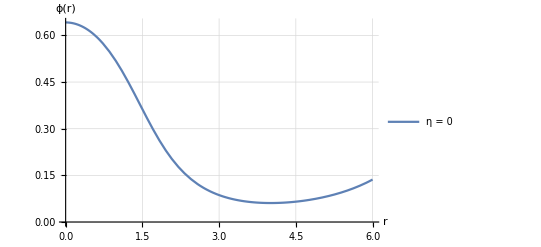

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,6},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
a=SeidelEqsList[[1]]/.(SeidelBCList[[1]]/.rMin-> r/.Equal-> Rule)//Simplify
```

{φ''[r]==(-1.59848×10^-8+0.000376697 r-1.2819 r^2+(-0.000113009+1.13009 r-0.000188349 r^2) gg'[r]+0.000113009 r NN''[r])/(3.64986×10^-9-0.0000483697 r+1. r^2),(1.71874×10^-8)/r+1. r==0.000271874,gg'[r]==-(1.85955×10^-9)/r+0.557866 r+0.0000843399 φ''[r]}

```mathematica
NSolve[a[[2]],r]
```

{{r→0.000171874},{r→0.0001}}

### data

```mathematica
Bs={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032736825266425024546711200243289808219829642490431642279`30.,150,30,0,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065835949573696846177350275907531973318828825330502424441`30.,100.0700000000034,30,0,0.01`30.},
(*{0.0030000000000000000624500451351650553988292813301086425781`30.,1.0099321063764611044831211129554904282201732712564989924431`30.,60.06999999999989,30,0,0.01`30.},*){0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106016081544170002223179530436890442542455237351362029585`30.,60.069999999999716,30,0,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.011954987515376924431307884387624283415146181352994858571`30.,60.06999999999983,30,0,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133129876708166055894180393211253105701470308974698752991`30.,60.06999999999994,30,0,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146771488855626293463551590407140550506148030107667068478`30.,60.0699999999996,30,0,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160472144488105647605014533469701953013217092525177775997`30.,60.06999999999983,30,0,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174231843605604118318569222398937313222677496227230875547`30.,60.069999999999716,30,0,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.018344006016054199414870367560587149924344885221216827631`30.,60.06999999999949,30,0,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269905817532166681635218399975813079183506459912678110413`30.,60.06999999999966,30,0,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.035877489321508490142804696249468742602628523741259414237`30.,60.06999999999926,30,0,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0450121304801593362174921948526086434039261176265345198999`30.,60.06999999999977,30,0,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0544028365789439100604072456968878003943835446661742016872`30.,50.06999999999977,30,0,0.01`30.},
{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0640581996429191519093299377975697251357036014120390453319`30.,50.06999999999989,30,0,0.01`30.},
{0.02026666666666666893892312373282038606703281402587890625`30.,1.0739868036134406465836717132219519480499393153800694440886`30.,40.06999999999994,30,0,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0841977627770874465590274159289713584768273016454656708576`30.,40.06999999999989,30,0,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0947006056786406716104757733107748507119282202911661427939`30.,40.06999999999994,30,0,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1055050253841343332553983559482949272163299758359577149797`30.,40.06999999999994,30,0,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.116621675308330270834470692444677922878711745038039017396`30.,40.06999999999989,30,0,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1280614286283593470397314504385750221800343992547902878813`30.,40.06999999999989,30,0,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.139835246169145591954234162767783603568587105141681801049`30.,40.06999999999989,30,0,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1519550542739285921023498946308235325655241567194072317374`30.,40.06999999999994,30,0,0.01`30.},{0.04,1.16447077028579,20.,30.,0.,1.*^-8},{0.042,1.174863039742705,20.,30.,0.,1.*^-8},{0.044,1.185506651020017,30.,30.,0.,1.*^-8},{0.046,1.196408378494969,30.,30.,0.,1.*^-8},{0.048,1.207576510035849,20.,30.,0.,1.*^-8},{0.05,1.219018571342151,20.,30.,0.,1.*^-8},{0.052,1.230742623941348,20.,30.,0.,1.*^-8},{0.054,1.242757501645907,20.,30.,0.,1.*^-8},{0.056,1.255071652560727,20.,30.,0.,1.*^-8},{0.058,1.267694320796101,18.,30.,0.,1.*^-8},{0.06,1.28063495884173,15.,30.,0.,1.*^-8},{0.07,1.350463702269447,30.,30.,0.,1.*^-8},{0.08,1.429880054976501,23.,14.,0.,1.*^-8},{0.09,1.520545101912098,14.,30.,0.,1.*^-8},{0.1,1.624469884859628,14.,30.,0.,1.*^-8},{0.11,1.7441016166994885,20.,30.,0.,1.*^-8},{0.13,2.0430621612059983,13.,30.,0.,1.*^-8},{0.15,2.449966765699886,13.,30.,0.,1.*^-8},{0.152,2.4958022244291476,18.,30.,0.,0.01},{0.1592,2.68250370388174,20.070000000000014,30.,0.,0.01},{0.16,2.7080677018789943,19.,30.,0.,1.*^-8},{0.1664,2.892505947790201,20.070000000000014,30.,0.,0.01},{0.17,3.012458355733277,19.,30.,0.,1.*^-8},{0.1736,3.1289332343242386,20.070000000000014,30.,0.,0.01},{0.1808,3.3952169283467635,20.070000000000014,30.,0.,0.01},{0.188,3.695071314017931,20.070000000000014,30.,0.,0.01},{0.19,3.7975050018636938,14.,30.,0.,1.*^-8},{0.2,4.300155639648437,13.1,30.,0.,1.*^-8},{0.22,5.590762832128472,13.,30.,0.,1.*^-8},{0.25,8.503837558382656,14.,30.,0.,1.*^-8},{0.3,18.2904052734375,12.,30.,0.,1.*^-8}};
```

```mathematica
Etam03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032730022983853821303561268400154449192330540462007821894`30.,176,30,-0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.0065799461494501541819545258672931154925138382964240697206`30.,143.06999999999994,30,-0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0105943416790243250634535468193862502128431243530754541181`30.,100.0699999999999,30,-0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119435729045454536876212778596582299573849385228739913253`30.,100.06999999999961,30,-0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0132984695633800182415892718524422714436652423088313236591`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146590437860911903802235097985129008338724016213804323155`30.,80.06999999999915,30,-0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160253253877096582115357548591261857814275199545917458729`30.,80.06999999999984,30,-0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0173973026377315444471279362823125258980993434747326366936`30.,80.06999999999967,30,-0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183150153769131991571518995362149003828917859756419496397`30.,60.07000000000004,30,-0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0269263755618292145423183946289692435686159289330276139799`30.,60.07000000000006,30,-0.3,0.01`30.},{0.010399999999999999522604099411182687617838382720947265625`30.,1.0357611351366596528899535652699588110204099697561632096197`30.,60.070000000000086,30,-0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0448244655178519680863143082528859157866491006846278098122`30.,40.07000000000006,30,-0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0541220290213564021949714955210224784050680990868943946814`30.,40.070000000000086,30,-0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0636597256309179944411342786339009210780830398717868154977`30.,40.07000000000003,30,-0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0734435644283601774482809738414173414128302822511850722735`30.,40.070000000000014,30,-0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0834785123089794941487036756039294065246864270529506062805`30.,30.070000000000057,30,-0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0937719913321628699577013704919345685229691613831570173172`30.,30.070000000000043,30,-0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1043295288862257261817553792071962775007266983682644300298`30.,30.07000000000003,30,-0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1151582315406098693728822748887597290740176703615252730931`30.,30.070000000000043,30,-0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1262643062990049786714509631897150308062350600512233133244`30.,30.070000000000086,30,-0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1376546774953322837776033245204343009113739124807627611112`30.,30.070000000000043,30,-0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1493366975098440465531281552752161605622573266044246685014`30.,30.070000000000014,30,-0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1613171191571093532766674680202811916996775593884803305847`30.,25.070000000000043,30,-0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1712552203463037939013152569966505293455323221483686822163`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1813986808106753382131971807855089525645575441402093955292`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.1917514159436011485560156122020326900257934877286827352648`30.,25.070000000000014,30,-0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.202317477866481081831506975175578727589897694281680023029`30.,25.070000000000057,30,-0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2131016365228341413710864619849530263735184199339506289635`30.,25.070000000000014,30,-0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2241078555524592470578757532998621410674823273464404337253`30.,20.070000000000014,30,-0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2353408700883620253504352919523043769256754694902070089369`30.,20.070000000000014,30,-0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2468063193200097260379598183440923077908036205538737639122`30.,20.070000000000014,30,-0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2585051522457477882765577651895613929402408155257925063127`30.,20.070000000000057,30,-0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2704460851777564870592641148577739837575362557779996688086`30.,20.070000000000014,30,-0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3339336275418824559937050199198665006870666414577333999835`30.,20.070000000000043,30,-0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4042096353786290789248800359620966596130197518832230960207`30.,20.07000000000003,30,-0.3,0.01`30.},{0.0899999999999999966693309261245303787291049957275390625`30.,1.4819868621430601038800347003539114991415719914690908851582`30.,15.069999999999991,30,-0.3,0.01`30.},{0.1000000000000000055511151231257827021181583404541015625`30.,1.568058291901689602300724247754550853345264240894827226558`30.,15.069999999999991,30,-0.3,0.01`30.},(*{0.11,1.6636919016,10,30,-0.3,0.001},*){0.12,1.769419016,10,30,-0.3,0.0001},{0.125,1.8264646898,10,30,-0.3,0.0001}};
```

```mathematica
Eta03={{0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032747602904357822958525382597852130477539843953535922548`30.,150.06999999999954,30,0.3,0.01`30.},{0.0020000000000000000416333634234433702658861875534057617188`30.,1.006587190830295712342626299746756157263233944307168751162`30.,150.06999999999965,30,0.3,0.01`30.},{0.0032000000000000001533495552763497471460141241550445556641`30.,1.0106135330775051308337193616691758995562055419078988204955`30.,100.06999999999967,30,0.3,0.01`30.},{0.0035999999999999999014677065645173570374026894569396972656`30.,1.0119682068798921124133486603238272436932905635028540096008`30.,100.06999999999978,30,0.3,0.01`30.},{0.0040000000000000000832667268468867405317723751068115234375`30.,1.0133293038760258846086468140797681462103989566478486313442`30.,100.06999999999972,30,0.3,0.01`30.},{0.0044000000000000002650657471292561240261420607566833496094`30.,1.0146967564929747512286294937377356381064430025087455473673`30.,80.06999999999961,30,0.3,0.01`30.},{0.0047999999999999995795030294232219603145495057106018066406`30.,1.0160706724574301490103591148793707563623070184230131271298`30.,80.06999999999955,30,0.3,0.01`30.},{0.0051999999999999997613020497055913438089191913604736328125`30.,1.0174511269519148729364514180090273228767602661288221671552`30.,80.06999999999944,30,0.3,0.01`30.},{0.0054666666666666665491680632271709328051656484603881835938`30.,1.0183750368982948484340133007636535036404359122214605940388`30.,80.06999999999978,30,0.3,0.01`30.},{0.00793333333333333390324781930758035741746425628662109375`30.,1.0270620626739372175991170353413084032725278239199563813585`30.,50.0699999999999,30,0.3,0.01`30.},{0.0128666666666666668766838554915921122301369905471801757812`30.,1.0452331893360278159376986654537167344356200642107877991278`30.,50.070000000000014,30,0.3,0.01`30.},{0.0153333333333333324960401355951944424305111169815063476562`30.,1.0547417281509326771552611615751772670919479566618999566254`30.,50.070000000000014,30,0.3,0.01`30.},{0.0177999999999999998501198916756038670428097248077392578125`30.,1.0645495993013036086336387560942795983083958695831124499407`30.,50.07000000000004,30,0.3,0.01`30.},{0.02026666666666666893892312373282038606703281402587890625`30.,1.0746712086700651575726740746753749142136670662247275356212`30.,50.07000000000004,30,0.3,0.01`30.},{0.0227333333333333310888324518828085274435579776763916015625`30.,1.0851212609390880297287722869685471972013459277787175118159`30.,40.07000000000003,30,0.3,0.01`30.},{0.02520000000000000017763568394002504646778106689453125`30.,1.0959154561720432335212371035209763692867756832564594175447`30.,30.070000000000086,30,0.3,0.01`30.},{0.027666666666666665796991964043627376668155193328857421875`30.,1.1070703551193921976418942252581703271814496905127694565301`30.,30.070000000000043,30,0.3,0.01`30.},{0.03013333333333333141634824414722970686852931976318359375`30.,1.1186040462662582885349815928631109030514576825284162375959`30.,30.07000000000003,30,0.3,0.01`30.},{0.03260000000000000397459842815806041471660137176513671875`30.,1.1305349179069105638012714775273376389882941944882695067313`30.,30.070000000000043,30,0.3,0.01`30.},{0.035066666666666669593954708261662744916975498199462890625`30.,1.1428831427916503201534346814971767605445479027011924911601`30.,30.070000000000057,30,0.3,0.01`30.},{0.0375333333333333352133109883652650751173496246337890625`30.,1.1556698224912977065016307346669602679022684213484705737934`30.,30.07000000000003,30,0.3,0.01`30.},{0.040000000000000000832667268468867405317723751068115234375`30.,1.1689171199979080032119261527870007701326835562703853003441`30.,30.070000000000014,30,0.3,0.01`30.},{0.042000000000000002609024107869117869995534420013427734375`30.,1.1800129928475641088474673691058090445615304360793544283767`30.,30.07000000000003,30,0.3,0.01`30.},{0.04399999999999999744648704336213995702564716339111328125`30.,1.1914403962458349959447498771508768665604517727419616146908`30.,30.070000000000057,30,0.3,0.01`30.},{0.04599999999999999922284388276239042170345783233642578125`30.,1.2032134956471430853168669822679894194442516499892908783418`30.,30.070000000000043,30,0.3,0.01`30.},{0.04800000000000000099920072216264088638126850128173828125`30.,1.2153470233010243679027886639019492347325775632141056433397`30.,30.070000000000014,30,0.3,0.01`30.},{0.05000000000000000277555756156289135105907917022705078125`30.,1.2278559583314948013805558426522668852956363086067580219955`30.,30.070000000000014,30,0.3,0.01`30.},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2407566070071718498545661063138107972881667880011991720547`30.,30.070000000000014,30,0.3,0.01`30.},{0.053999999999999999389377336456163902767002582550048828125`30.,1.2540651459427390675364701004624271833808006094226708408704`30.,30.070000000000014,30,0.3,0.01`30.},{0.056000000000000001165734175856414367444813251495361328125`30.,1.2677985898558739538332765574039556632092672783922480933471`30.,30.070000000000014,30,0.3,0.01`30.},{0.058000000000000002942091015256664832122623920440673828125`30.,1.2819747100665400163858990186123352572899140050258193779936`30.,30.070000000000014,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115045798694441587962499183915647859786794512963160083`30.,30.07000000000003,30,0.3,0.01`30.},{0.059999999999999997779553950749686919152736663818359375`30.,1.2966115874051752575499979156944799614751963526555253479636`30.,20.070000000000014,30,0.3,0.01`30.},{0.070000000000000006661338147750939242541790008544921875`30.,1.3773398393006772073807982193090534048461327238126206049275`30.,20.07000000000003,30,0.3,0.01`30.},{0.08000000000000000166533453693773481063544750213623046875`30.,1.4719135834424746974380579827404594012894102799158426753109`30.,20.070000000000057,30,0.3,0.01`30.}};
```

### Checking

Mass

```mathematica
Dat=Eta03;
```

```mathematica
Table[
AA=Dat[[i]];
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec]*√(8π);
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
c4=-1/2;
L3=(1/η)^(1/3);
N0=1;

(*s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; (*φ*)

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{AA[[1]](*Evaluate[M[rMax]/.s]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[Dat]}](*Length[Dat]*)
```

## N_95

d^3 x=r^2 Sin[θ]dr dθ dϕ=4π r^2 dr

Q=∫√-g j^0 ⅆ^3 x

```mathematica
(*j0H[r_]:=2 w (ϕ[r]^2-(4 d Mp NN[r]^3 ϕ[r] ϕ'[r]^3 (gg[r] ϕ[r] NN'[r] ϕ'[r]+NN[r] (gg[r] ϕ'[r]^2+ϕ[r] (gg'[r] ϕ'[r]-gg[r] ϕ''[r]))))/(Λ^3 r gg[r]^3 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)-(2 c Mp (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]));*)
```

```mathematica
j0H[r_]:=2 w (ϕ[r]^2-(2 c (gg[r]^3 NN[r] ϕ[r]^2+r NN[r] ϕ[r] gg'[r] (2 ϕ[r]-r ϕ'[r])+gg[r] (-r^2 ϕ[r] NN'[r] ϕ'[r]+NN[r] (-ϕ[r]^2+r^2 ϕ'[r]^2+r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))))/(Λ^3 r^2 gg[r]^3 NN[r]));
```

```mathematica
data=Eta03;
```

```mathematica
dataE={};
```

```mathematica
Clear[w, s0,s1,AA,rMax,rlim,c4];
```

```mathematica
Do[
AA=data[[i]];

Print[i];

SeidelBCList={};
Clear[rMin,ϕ0,r,c4,α,η,L1,w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0-(N0 rMin^2 (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(6 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L3^3 mS^2 N0^4 ϕ0^2-L3^3 N0^2 w^2 ϕ0^2+12 c4 Mp w^4 ϕ0^2))/(6 Mp N0^2 (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)),φ[rMin]==ϕ0-(rMin^2 w^2 ϕ0)/(2 N0^2),NN'[rMin]==-(N0 rMin (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(3 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),φ'[rMin]==-(rMin w^2 ϕ0)/N0^2}];

(* Solving *)
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec]*√(8π);
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
c4=-1/2;
L3=(1/η)^(1/3);
N0=1;


s0=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(*Print[s0];*)

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s0]*Evaluate[gg[rMax]/.s0]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

(* Solving again *)
SeidelBCList={};
Clear[ w,N0];

AppendTo[SeidelBCList,{NN[rMin]==N0-(N0 rMin^2 (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(6 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L3^3 mS^2 N0^4 ϕ0^2-L3^3 N0^2 w^2 ϕ0^2+12 c4 Mp w^4 ϕ0^2))/(6 Mp N0^2 (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)),φ[rMin]==ϕ0-(rMin^2 w^2 ϕ0)/(2 N0^2),NN'[rMin]==-(N0 rMin (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(3 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),φ'[rMin]==-(rMin w^2 ϕ0)/N0^2}];

N0= B[[1,1,1,2]];
w=w2;

s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}(*,MaxSteps->10^6,MaxStepSize->0.0001,MaxStepFraction->0.001*),Method->{"EquationSimplification"->"Residual"}];

(*Print[s1];*)
Clear[rlim, ϕ20,r0,enc];
ϕ20=ϕ0;
r0=rMin;
enc=0;
Do[
temp=ϕ20;
rtemp=r0;
If[Evaluate[φ[rB]/.s1][[1]]>temp||Evaluate[φ[rB]/.s1][[1]]<0,
(*Print[temp, "no cumplió ",Evaluate[φ[rB]/.s1][[1]]];*)
rlim=N[rtemp];
enc=1;
Break[],
ϕ20=Evaluate[φ[rB]/.s1][[1]];
r0=rB
],
{rB,rMin,rMax,0.001}];
If[enc==0,rlim=rMax];

Print[rlim, " ", rMax];

Print[
Plot[Evaluate[φ[r]/.s1],{r,rMin,rlim},PlotLegends->{Evaluate[φ[rMax]/.s1]}]
];
NE=NIntegrate[((Evaluate[gg[r]/NN[r]]/.s1)*Evaluate[j0H[r]/.s1])r^2 Sin[θ],{r,rMin,rlim},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"];N95=NE[[1]];(*0.95*)
(*Print[N95];*)
AppendTo[dataE,{ϕ0,N95}];
,{i,1,Length[data]}]
```

```mathematica
dataE
```

```mathematica
NvsrhoEta0={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6344689243669515},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.093294025651763},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.389143311712792},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.738511485711928},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.076240041515835},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.391507895830112},{0.024063631436457602715132155045322590836670091247431265286`30.,7.691061021525971},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.9749699499700295},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.15611678513496},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.604579160671012},{0.0521378681123248080569397927063501881413711934354659082782`30.,10.749547997536158},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.688882097927479},{0.076869933755350677876517861520956946722713119839664403182`30.,12.474349996099205},{0.0892359665768636171346138094778961420038894078404933176173`30.,13.138956273790598},{0.1016019993983765650893235845341069692660763454387815660195`30.,13.705803165017066},{0.1139680322198894782575780511932312686042206846472324785541`30.,14.190997254523827},{0.1263340650414024262122878262494420958664076222455207269563`30.,14.606872958287264},{0.1387000978629153567737699471071096591665732606488903074248`30.,14.96334212510879},{0.1510661306844282873352520679647772224667388990522598878932`30.,15.267346230213944},{0.1634321635059412526831894972195313136909471358454668042291`30.,15.524853057614093},{0.1757981963274541832446716180771988769911127742488363846976`30.,15.7415387574424},{0.188164229148967113806153738934866440291278412652205965166`30.,15.921433794992211},{0.2005302619704800443676358597925340035914440510555755456344`30.,16.0691069854778},{0.2105567750690040552826314798814323357520269032058136568832`30.,16.166172523521126},{0.2205832881675280314111717915732441399885671569662144322642`30.,16.245057512177937},{0.2306098012660520423261674116621424721491500091164525435128`30.,16.307558876622075},{0.2406363143645760532411630317510408043097328612666906547614`30.,16.354148176203985},{0.2506628274631000641561586518399391364703157134169287660099`30.,16.386371012830114},{0.2606893405616240402846989635317509407068559671773295413911`30.,16.405402427769854},{0.2707158536601480511996945836206492728674388193275676526397`30.,16.411620497365075},{0.2807423667586720621146902037095476050280216714778057638883`30.,16.406334088029773},{0.2907688798571960730296858237984459371886045236280438751368`30.,16.390071647944378},{0.300795392955720049158226135490257741425144777388444650518`30.,16.36359386836756},{0.3509279584483401037332042359347494022280590381396352067611`30.,16.099649623751525},{0.40106052394096008873527171958506800718`14.,15.660987806796697},{0.451193089433580073737339203235386612137717166082666975777`30.,15.095324704743305},{0.50132565492620012831231730367987827294063142683385753202`30.,14.438988649163349},{0.551458220418820113314384787330196877895460490805373416528`30.,13.719937361701037},{0.651723351404060152891430371425007143653203815528079857279`30.,12.182956507770463},{0.751988482389300122895565338725644353562861943471111626295`30.,10.637500487422159},{0.7620149954878241338105609588145426857234447956213497375436`30.,10.495296258856612},{0.7981104426425106009337094378522459038407771420740768067326`30.,9.97002420254333},{0.8021210478819201774705434391701360143657762042223021825381`30.,9.904329626336184},{0.8342058897971969289110366833016030102619390949674545324515`30.,9.469426475291582},{0.8522536133745402320455215396146276751686904649734927387811`30.,9.219914535133883},{0.8703013369518833960341851623393062283792714414201816016404`30.,8.999903777649925},{0.9063967841065697240115124077886633348004333943135593273595`30.,8.568016765185737},{0.9424922312612561911346608868263665529177657407662863965484`30.,8.180216364800447},{0.952518744359780202049656506915264885078348592916524507797`30.,8.067685505407704},{1.00265130985240025662463460735975654588126285366771506404`30.,7.6347647044728015},{1.1029164408376402266287695746603937557909209816107468330559`30.,7.128355030106395},{1.2533141373155002512078826424055226265034933703049691583149`30.,7.263694171435854},{1.5039769647786002457911306774512887071257238869422232525899`30.,8.190294741941976}};
```

```mathematica
NvsrhoEtam03={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.642116070515988},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.119834121965324},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.422528050315193},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.794674383627218},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.142836693226501},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.471214799991102},{0.024063631436457602715132155045322590836670091247431265286`30.,7.782047584910851},{0.0260689340561624040284698963531750940706855967177329541391`30.,8.077502305372047},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.267767008910008},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.79462555218894},{0.0521378681123248080569397927063501881413711934354659082782`30.,11.028620606333789},{0.0645039009338377473150357406632893834225474814362948227135`30.,12.064506999720814},{0.076869933755350677876517861520956946722713119839664403182`30.,12.953438042420562},{0.0892359665768636171346138094778961420038894078404933176173`30.,13.726754519641812},{0.1016019993983765650893235845341069692660763454387815660195`30.,14.40518118394113},{0.1139680322198894782575780511932312686042206846472324785541`30.,15.007664522436096},{0.1263340650414024262122878262494420958664076222455207269563`30.,15.542169124717958},{0.1387000978629153567737699471071096591665732606488903074248`30.,16.019614084015583},{0.1510661306844282873352520679647772224667388990522598878932`30.,16.44565919216556},{0.1634321635059412526831894972195313136909471358454668042291`30.,16.82737642494838},{0.1757981963274541832446716180771988769911127742488363846976`30.,17.16944795558062},{0.188164229148967113806153738934866440291278412652205965166`30.,17.47500592564762},{0.2005302619704800443676358597925340035914440510555755456344`30.,17.74855974625498},{0.2105567750690040552826314798814323357520269032058136568832`30.,17.94861252083772},{0.2205832881675280314111717915732441399885671569662144322642`30.,18.130643062137064},{0.2306098012660520423261674116621424721491500091164525435128`30.,18.295968729717792},{0.2406363143645760532411630317510408043097328612666906547614`30.,18.445986807080914},{0.2506628274631000641561586518399391364703157134169287660099`30.,18.581195034882064},{0.2606893405616240402846989635317509407068559671773295413911`30.,18.702951683893186},{0.2707158536601480511996945836206492728674388193275676526397`30.,18.812034352390068},{0.2807423667586720621146902037095476050280216714778057638883`30.,18.907711314767635},{0.2907688798571960730296858237984459371886045236280438751368`30.,18.994653411738653},{0.300795392955720049158226135490257741425144777388444650518`30.,19.06968020728877},{0.3509279584483401037332042359347494022280590381396352067611`30.,19.306906383051558},{0.401060523940960088735271719585068007182888102111151091269`30.,19.35416517832566},{0.451193089433580073737339203235386612137717166082666975777`30.,19.254283721404004},{0.50132565492620012831231730367987827294063142683385753202`30.,19.037717683191},{0.6015907859114400983164522709805154828502895547768893010359`30.,18.336188979636464},{0.6266570686577501256039413212027613132517466851524845791574`30.,18.11597970959033}};
```

```mathematica
NvsrhoEta03={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6239468065932514},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.069093617938071},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.322551485812769},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.674944033299222},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.002955361615294},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.310722553778586},{0.024063631436457602715132155045322590836670091247431265286`30.,7.6004604614183044},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.873450749264854},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.048233081883287},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.420106645611108},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.326339022655747},{0.076869933755350677876517861520956946722713119839664403182`30.,12.014377834788483},{0.0892359665768636171346138094778961420038894078404933176173`30.,12.57889690556032},{0.1016019993983765650893235845341069692660763454387815660195`30.,13.042028115338628},{0.1139680322198894782575780511932312686042206846472324785541`30.,13.421381519669515},{0.1263340650414024262122878262494420958664076222455207269563`30.,13.72980958469263},{0.1387000978629153567737699471071096591665732606488903074248`30.,13.977553412704344},{0.1510661306844282873352520679647772224667388990522598878932`30.,14.171757778070834},{0.1634321635059412526831894972195313136909471358454668042291`30.,14.319660345905895},{0.1757981963274541832446716180771988769911127742488363846976`30.,14.425993583586267},{0.188164229148967113806153738934866440291278412652205965166`30.,14.495346423822546},{0.2005302619704800443676358597925340035914440510555755456344`30.,14.531942880681376},{0.2105567750690040552826314798814323357520269032058136568832`30.,14.53937054029072},{0.2205832881675280314111717915732441399885671569662144322642`30.,14.52900851657547},{0.2306098012660520423261674116621424721491500091164525435128`30.,14.502294252030222},{0.2406363143645760532411630317510408043097328612666906547614`30.,14.460174722926267},{0.2506628274631000641561586518399391364703157134169287660099`30.,14.403931341473585},{0.2606893405616240402846989635317509407068559671773295413911`30.,14.334395415611375},{0.2707158536601480511996945836206492728674388193275676526397`30.,14.252750801912315},{0.2807423667586720621146902037095476050280216714778057638883`30.,14.160155312218661},{0.2907688798571960730296858237984459371886045236280438751368`30.,14.05698152623134},{0.300795392955720049158226135490257741425144777388444650518`30.,13.944439081329474},{0.300795392955720049158226135490257741425144777388444650518`30.,13.944381158939917},{0.3509279584483401037332042359347494022280590381396352067611`30.,13.266461997321093},{0.401060523940960088735271719585068007182888102111151091269`30.,12.48043576645446}};
```

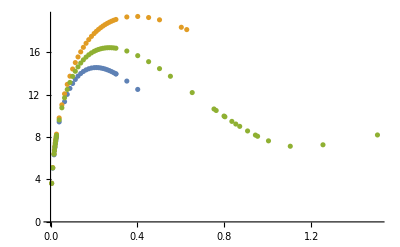

```mathematica
ListPlot[{NvsrhoEta03,NvsrhoEtam03,NvsrhoEta0},AxesOrigin->{0,0},PlotLegends->Automatic;FrameLabel->{"ρ0","N|M"},PlotRange->All]
```

```mathematica
PlotTheme->"Scientific"
```

```mathematica
Export["N_BS.dat",NvsrhoEta0]
```

N_BS.dat

```mathematica
Export["NvsrhoEta03.dat",NvsrhoEta03]
Export["NvsrhoEtam03.dat",NvsrhoEtam03]
```

NvsrhoEta03.dat

NvsrhoEtam03.dat

## Masa

```mathematica
SeidelBCList={};
Clear[rMin,ϕ0,r,c4,α,η,L1,w,N0,mS,k];

AppendTo[SeidelBCList,{NN[rMin]==N0-(N0 rMin^2 (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(6 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L3^3 mS^2 N0^4 ϕ0^2-L3^3 N0^2 w^2 ϕ0^2+12 c4 Mp w^4 ϕ0^2))/(6 Mp N0^2 (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)),φ[rMin]==ϕ0-(rMin^2 w^2 ϕ0)/(2 N0^2),NN'[rMin]==-(N0 rMin (L3^6 Mp mS^2 N0^4 ϕ0^2-2 L3^6 Mp N0^2 w^2 ϕ0^2+12 c4 L3^3 Mp^2 w^4 ϕ0^2+4 c4 L3^3 mS^2 N0^2 w^2 ϕ0^4-2 c4 L3^3 w^4 ϕ0^4))/(3 Mp (L3^3 Mp N0^2+2 c4 w^2 ϕ0^2)^2),φ'[rMin]==-(rMin w^2 ϕ0)/N0^2}];
```

```mathematica
mvsr={};
phivswf={};
wfvsm={};
stop2=0;

For[j=1,j<Length[Bs]+1,j++,
Print[j];

AA=Bs[[j]];
prec=AA[[4]];
η= Abs[AA[[5]]]; 
Mp=1;mS=1;N0=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec]*√(8π);
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
c4=0;
L3=1(*(1/η)^(1/3)*);
N0=1;


Clear[s,M95, M];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]8π; 

M95=0.95M[rMax][[1]];

(* comprobando ϕ pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<4*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Break[]];

(* calculando radio *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];

Print[rad];
Print["masa95 = ", M95];

(* calculando frecuencia*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

AppendTo[mvsr,{rad[[2]],M[rMax][[1]]}];
AppendTo[phivswf,{ϕ0,M[rMax][[1]]}];
AppendTo[wfvsm,{w2,M95}];
](* FOR *)
(* Resultados *)

mvsr
phivswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full]}]
Show[{ListPlot[phivswf,PlotRange->Full]}]
Show[{ListPlot[wfvsm,PlotRange->Full]}]
```

```mathematica
MvsrhoEta0={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6328627006313905},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.082070127778417},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.366909747109032},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.711464105023235},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.044978836694404},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.355499301452053},{0.024063631436457602715132155045322590836670091247431265286`30.,7.650400274177276},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.9294471357651375},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.107334581306757},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.523540178234157},{0.0521378681123248080569397927063501881413711934354659082782`30.,10.673210177382693},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.897979780775408},{0.076869933755350677876517861520956946722713119839664403182`30.,12.357746132480019},{0.0892359665768636171346138094778961420038894078404933176173`30.,12.942240299452099},{0.1016019993983765650893235845341069692660763454387815660195`30.,13.448731516270238},{0.1139680322198894782575780511932312686042206846472324785541`30.,13.936642806525098},{0.1263340650414024262122878262494420958664076222455207269563`30.,14.516060023810821},{0.1387000978629153567737699471071096591665732606488903074248`30.,14.697887942766961},{0.1510661306844282873352520679647772224667388990522598878932`30.,14.928837709759483},{0.1634321635059412526831894972195313136909471358454668042291`30.,15.195899032404938},{0.1757981963274541832446716180771988769911127742488363846976`30.,15.340432311303124},{0.2005302619704800443676358597925340035914440510555755456344`30.,15.609676986397568},{0.2105567750690040552826314798814323357520269032058136568832`30.,15.695351690497573},{0.2205832881675280314111717915732441399885671569662144322642`30.,15.764664732424825},{0.2306098012660520423261674116621424721491500091164525435128`30.,15.857562696139526},{0.2406363143645760532411630317510408043097328612666906547614`30.,15.859403393657516},{0.2506628274631000641561586518399391364703157134169287660099`30.,15.88724966856022},{0.2606893405616240402846989635317509407068559671773295413911`30.,15.903562231251215},{0.2707158536601480511996945836206492728674388193275676526397`30.,15.908929743835072},{0.2807423667586720621146902037095476050280216714778057638883`30.,15.904401941579051},{0.2907688798571960730296858237984459371886045236280438751368`30.,15.890659488439866},{0.300795392955720049158226135490257741425144777388444650518`30.,15.868326636234166},{0.3509279584483401037332042359347494022280590381396352067611`30.,15.837848924583763},{0.40106052394096008873527171958506800718`14.,15.29471342277625},{0.451193089433580073737339203235386612137717166082666975777`30.,14.83766598303419},{0.50132565492620012831231730367987827294063142683385753202`30.,14.319171373414953},{0.551458220418820113314384787330196877895460490805373416528`30.,13.758073328161377},{0.651723351404060152891430371425007143653203815528079857279`30.,12.571642879185461},{0.751988482389300122895565338725644353562861943471111626295`30.,11.384623131343705},{0.7620149954878241338105609588145426857234447956213497375436`30.,11.275141431617783},{0.7981104426425106009337094378522459038407771420740768067326`30.,10.86972374904789},{0.8021210478819201774705434391701360143657762042223021825381`30.,10.818832407324988},{0.8342058897971969289110366833016030102619390949674545324515`30.,10.481245539903998},{0.8522536133745402320455215396146276751686904649734927387811`30.,10.286707917768963},{0.8703013369518833960341851623393062283792714414201816016404`30.,10.114913801052868},{0.9063967841065697240115124077886633348004333943135593273595`30.,9.774502245962568},{0.9424922312612561911346608868263665529177657407662863965484`30.,9.466227702494441},{0.952518744359780202049656506915264885078348592916524507797`30.,9.376184614301476},{1.00265130985240025662463460735975654588126285366771506404`30.,9.026900146656342},{1.1029164408376402266287695746603937557909209816107468330559`30.,8.61027335055167},{1.2533141373155002512078826424055226265034933703049691583149`30.,8.726448249258695},{1.5039769647786002457911306774512887071257238869422232525899`30.,9.517769597308938}};
```

```mathematica
MvsrhoEtam03={{0.0050132565492620011091908964948133500897861012763893886408`30.,4.202952151731235},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.2944964680443904},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.418816206739276},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.851168253844012},{0.0200530261970480044367635859792534003591444051055575545634`30.,7.1119763432739935},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.438267473934255},{0.024063631436457602715132155045322590836670091247431265286`30.,7.742132048155006},{0.0260689340561624040284698963531750940706855967177329541391`30.,8.0308845502447},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.217620099716408},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.712350402699176},{0.0521378681123248080569397927063501881413711934354659082782`30.,10.957346811544141},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.90084511488882},{0.076869933755350677876517861520956946722713119839664403182`30.,12.749214732588115},{0.0892359665768636171346138094778961420038894078404933176173`30.,13.479033705443019},{0.1016019993983765650893235845341069692660763454387815660195`30.,14.151694987916988},{0.1139680322198894782575780511932312686042206846472324785541`30.,14.675733056008127},{0.1263340650414024262122878262494420958664076222455207269563`30.,15.168474140098414},{0.1387000978629153567737699471071096591665732606488903074248`30.,15.605602657714828},{0.1510661306844282873352520679647772224667388990522598878932`30.,15.991972135382428},{0.1634321635059412526831894972195313136909471358454668042291`30.,16.33599159741011},{0.1757981963274541832446716180771988769911127742488363846976`30.,16.643135533166912},{0.188164229148967113806153738934866440291278412652205965166`30.,16.911746235027532},{0.2005302619704800443676358597925340035914440510555755456344`30.,17.152029966179068},{0.2105567750690040552826314798814323357520269032058136568832`30.,17.32682718751706},{0.2205832881675280314111717915732441399885671569662144322642`30.,17.484404838789747},{0.2306098012660520423261674116621424721491500091164525435128`30.,17.626891988882253},{0.2406363143645760532411630317510408043097328612666906547614`30.,17.75560332159576},{0.2506628274631000641561586518399391364703157134169287660099`30.,17.87027708002521},{0.2606893405616240402846989635317509407068559671773295413911`30.,17.973185575035004},{0.2707158536601480511996945836206492728674388193275676526397`30.,18.064633217073137},{0.2807423667586720621146902037095476050280216714778057638883`30.,18.147300671677232},{0.2907688798571960730296858237984459371886045236280438751368`30.,18.216766802707745},{0.300795392955720049158226135490257741425144777388444650518`30.,18.278655526053527},{0.3509279584483401037332042359347494022280590381396352067611`30.,18.47133973589249},{0.401060523940960088735271719585068007182888102111151091269`30.,18.50896059688697},{0.451193089433580073737339203235386612137717166082666975777`30.,18.432741262618592},{0.50132565492620012831231730367987827294063142683385753202`30.,18.274042870425983},{0.6015907859114400983164522709805154828502895547768893010359`30.,17.788156533318663},{0.6266570686577501256039413212027613132517466851524845791574`30.,17.64868812835737}};
```

```mathematica
MvsrhoEta03={{0.0050132565492620011091908964948133500897861012763893886408`30.,3.6337228312414167},{0.0100265130985240022183817929896267001795722025527787772818`30.,5.081500565820376},{0.0160424209576384039842415601383663018863660565643190103491`30.,6.300202146712012},{0.0180477235773432031234258446714008971251288996352558657104`30.,6.655999114832328},{0.0200530261970480044367635859792534003591444051055575545634`30.,6.972540156885656},{0.0220583288167528057501013272871059035931599105758592434165`30.,7.275454007218195},{0.024063631436457602715132155045322590836670091247431265286`30.,7.5658679091769},{0.0260689340561624040284698963531750940706855967177329541391`30.,7.8317497098126205},{0.0274058024692989382373617238917434295600292670312674133744`30.,8.032702948691565},{0.0397718352908118774954576718486826248412055550320963278098`30.,9.342461213016968},{0.0645039009338377473150357406632893834225474814362948227135`30.,11.18506631701135},{0.076869933755350677876517861520956946722713119839664403182`30.,11.86693552832573},{0.0892359665768636171346138094778961420038894078404933176173`30.,12.554646921534863},{0.1016019993983765650893235845341069692660763454387815660195`30.,12.894574304857537},{0.1139680322198894782575780511932312686042206846472324785541`30.,13.180660795564993},{0.1263340650414024262122878262494420958664076222455207269563`30.,13.454649202362623},{0.1387000978629153567737699471071096591665732606488903074248`30.,13.682958807507456},{0.1510661306844282873352520679647772224667388990522598878932`30.,13.86106502776962},{0.1634321635059412526831894972195313136909471358454668042291`30.,13.99584028638309},{0.1757981963274541832446716180771988769911127742488363846976`30.,14.091866619118763},{0.188164229148967113806153738934866440291278412652205965166`30.,14.154274315820006},{0.2005302619704800443676358597925340035914440510555755456344`30.,14.187848673799868},{0.2105567750690040552826314798814323357520269032058136568832`30.,14.199893079024552},{0.2205832881675280314111717915732441399885671569662144322642`30.,14.189287574354863},{0.2306098012660520423261674116621424721491500091164525435128`30.,14.16165046265119},{0.2406363143645760532411630317510408043097328612666906547614`30.,14.1243183559879},{0.2506628274631000641561586518399391364703157134169287660099`30.,14.074452232545676},{0.2606893405616240402846989635317509407068559671773295413911`30.,14.016208056106294},{0.2707158536601480511996945836206492728674388193275676526397`30.,13.952708829613178},{0.2807423667586720621146902037095476050280216714778057638883`30.,13.864662351137566},{0.2907688798571960730296858237984459371886045236280438751368`30.,13.775501147866143},{0.300795392955720049158226135490257741425144777388444650518`30.,13.68247550767509},{0.300795392955720049158226135490257741425144777388444650518`30.,13.676205321461312},{0.3509279584483401037332042359347494022280590381396352067611`30.,13.09602371198277},{0.401060523940960088735271719585068007182888102111151091269`30.,12.42815486576404}};
```

```mathematica
RvsMEtam03={{172.75776736347984,4.202952151731235},{45.262197728432504,5.2944964680443904},{29.24202992184374,6.851168253844012},{26.46025788897577,7.1119763432739935},{25.222192120024598,7.438267473934255},{24.08634600876932,7.742132048155006},{23.087197888467365,8.0308845502447},{22.498877505872475,8.217620099716408},{18.52065018649201,9.712350402699176},{16.283466084989826,10.957346811544141},{14.265042347828377,11.90084511488882},{12.953555547754027,12.749214732588115},{11.910571098001352,13.479033705443019},{11.160664293807033,14.151694987916988},{10.351215610842752,14.675733056008127},{9.742697688958861,15.168474140098414},{9.2163259397788,15.605602657714828},{8.751058937765684,15.991972135382428},{8.339098509222866,16.33599159741011},{7.971792976763664,16.643135533166912},{7.632787009501339,16.911746235027532},{7.327507153479043,17.152029966179068},{7.099345119737948,17.32682718751706},{6.885381348789063,17.484404838789747},{6.685043410441418,17.626891988882253},{6.497129777447995,17.75560332159576},{6.31887538911124,17.87027708002521},{6.150848874937659,17.973185575035004},{5.99152063755641,18.064633217073137},{5.842541339359468,18.147300671677232},{5.696338789554429,18.216766802707745},{5.559050969384654,18.278655526053527},{4.957025931967305,18.47133973589249},{4.4611563260536995,18.50896059688697},{4.039903810884195,18.432741262618592},{3.674931025172215,18.274042870425983},{3.063079911440741,17.788156533318663},{2.9333965335204497,17.64868812835737}};
```

```mathematica
RvsMEta03={{54.06557649481324,3.6337228312414167},{38.258001211123926,5.081500565820376},{29.60070506255396,6.300202146712012},{27.969887244066292,6.655999114832328},{26.38933079884133,6.972540156885656},{25.11594275069632,7.275454007218195},{24.064903144516432,7.5658679091769},{23.05113820908081,7.8317497098126205},{22.752794640677614,8.032702948691565},{18.435662895428127,9.342461213016968},{14.19066569295133,11.18506631701135},{12.969341908366598,11.86693552832573},{11.251526064095499,12.894574304857537},{10.318051502772281,13.180660795564993},{9.68036418769926,13.454649202362623},{9.158838750934855,13.682958807507456},{8.701843505633539,13.86106502776962},{8.297784002119746,13.99584028638309},{7.936031288297268,14.091866619118763},{7.610751656073802,14.154274315820006},{7.318415899145724,14.187848673799868},{7.109599590823911,14.199893079024552},{6.903501936025862,14.189287574354863},{6.7071201518524814,14.16165046265119},{6.530263936903354,14.1243183559879},{6.364537250883956,14.074452232545676},{6.2144165188153595,14.016208056106294},{6.082786926198507,13.952708829613178},{5.934302802198803,13.864662351137566},{5.807380775806266,13.775501147866143},{5.695270975999259,13.68247550767509},{5.684800067603153,13.676205321461312},{5.197635374095975,13.09602371198277},{4.875401566111604,12.42815486576404}};
```

```mathematica
RvsMEta0={{53.54420398875108,3.6328627006313905},{37.64106430595025,5.082070127778417},{29.814058404008005,6.366909747109032},{27.927353490970727,6.711464105023235},{26.451164919920632,7.044978836694404},{25.155185568214495,7.355499301452053},{24.042498156118924,7.650400274177276},{23.05711848924741,7.9294471357651375},{22.460020873741467,8.107334581306757},{18.467178440734923,9.523540178234157},{16.185508560256295,10.673210177382693},{13.18662478539851,12.357746132480019},{11.960222305330236,12.942240299452099},{11.027255498562669,13.448731516270238},{10.412228338990149,13.936642806525098},{8.808210528375358,14.928837709759483},{8.465594448127314,15.195899032404938},{7.991872434382174,15.340432311303124},{7.317614895270514,15.609676986397568},{7.093239544185862,15.695351690497573},{6.884014004316706,15.764664732424825},{6.749637961822022,15.857562696139526},{6.504156037664138,15.859403393657516},{6.331314249309371,15.88724966856022},{6.1685353631781705,15.903562231251215},{6.014608647845447,15.908929743835072},{5.869012484747898,15.904401941579051},{5.730972782777869,15.890659488439866},{5.5997980817850355,15.868326636234166},{5.300313368686874,15.837848924583763},{4.5796400102994355,15.29471342277625},{4.201184164336634,14.83766598303419},{3.8900345130162575,14.319171373414953},{3.629309473783122,13.758073328161377},{3.225744354246993,12.571642879185461},{2.953650105328868,11.384623131343705},{2.9342124305338078,11.275141431617783},{2.8705160405855743,10.86972374904789},{2.8634231244642008,10.818832407324988},{2.8228505205446055,10.481245539903998},{2.804633277676073,10.286707917768963},{2.7928112802479252,10.114913801052868},{2.7795289683735938,9.774502245962568},{2.785502264493303,9.466227702494441},{2.79144566929839,9.376184614301476},{2.8425346098841655,9.026900146656342},{3.058574219170653,8.61027335055167},{3.490500042230311,8.726448249258695},{3.6418317329905445,9.517769597308938}};
```

```mathematica
Export["MvsrhoEta03.dat",MvsrhoEta03]
Export["MvsrhoEtam03.dat",MvsrhoEtam03]
```

MvsrhoEta03.dat

MvsrhoEtam03.dat

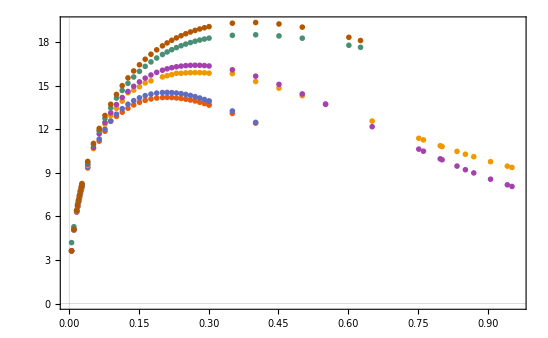

```mathematica
ListPlot[{MvsrhoEta03,NvsrhoEta03,MvsrhoEta0,NvsrhoEta0,MvsrhoEtam03,NvsrhoEtam03},Joined->False,PlotTheme->"Scientific"]
```

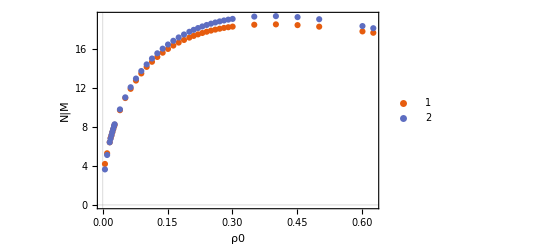

```mathematica
ListPlot[{MvsrhoEtam03,NvsrhoEtam03},AxesOrigin->{0,0},PlotTheme->"Scientific",PlotLegends->Automatic,FrameLabel->{"ρ0","N|M"},PlotRange->All]
```

```mathematica
Export["M_BS.dat",MvsrhoEta0]
```

M_BS.dat